## V2: Kay’s program do not work because of some extra simplifications he performs. Indeed, γ1 followed by γ2^+ cannot be substituted by γ1δχ directly: there is also an effective γg vertex I wrote a new program, which works as follows: generate a string of gamma interactions from the bottom to the top of the red line. There are 4 different vertices. Note that I split Gamma_1 into the one where the green line goes to one, and the fluctuating part. γ11: Subscript[Γ, 1]-vertex where the outgoing green line is set to 1 γ1δχ: Subscript[Γ, 1]-vertex where the outgoing green line is δχ γ2p: Subsuperscript[Γ, 2, +] γ2m: : Subsuperscript[Γ, 2, -] I offer all the different combinations to Mathematica. Then I count that at the end there are n+1 Gamma_1, and not more gamma_2 than I can possibly contract (they have \delta \chi fields). Whenever I see \gamma_11 \gamma_2^+, I replace by - gamma_1\chi (this does the integration of Laplace applied to a red line). Note the change in the gamma_1 vertex! What I got at 2-loop order is in the photo I mailed. There are two terms which are trees, and which I already threw out (boxed in the drawing). Then I find that playing at the upper right corner, there is a cancelation between (1)+(3), as long as we do not probe the red line. The only thing which remains is (4). This can now be contracted in all possible ways. Can you check the logic of this procedure, and write a code to redo it? (I used a Dot[] product in Mathematica.) Both in 1 and 2 loops, there is a single string which one needs then to contrast with interactions. That makes for some very decent simplification. I succeeded to run 3 loops, 13 diagrams (before cancellations at the last vertex).

```mathematica
Quit
```

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
SetDirectory["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\MathematicaFiles-LRW-DLA\\Routines\\"]
<<LRWDiagrams`
```

D:\Offline_Documents\University\PhD_Paris\PhD_work\Simulations\MathematicaFiles-LRW-DLA\Routines

# Field Theory tools

## SpaceVertices definition

### WITH POWER COUNTING

```mathematica
<<LRWDiagrams`
ClearAll[Vγ1,Vγ1δ,Vγ1δ1,Vγ1δ2,Vγ1Minus,Vγg,Vγ1gχMinus,Vγ1gψ,Vγ1gψMinus,Vγ2,Vγ21,Vγ22,Vγ2Minus,Vγ2Minus1,Vγ2Minus2,Vγ2gχ,Vγ2gχMinus,Vγ2gψ,Vγ2gψMinus,Vψψ,Vψχ,Vδψχ,Vχχ,g,b];

Vγ1[space_,time_]:= V[γ  ϕ[space,Subscript[t, time]](1)ϕs[space,Subscript[t, time+1]]ψs[space,Subscript[t, time+1]]];

Vγ1δ1[space_,time_]:= V[γ  ϕ[space,Subscript[t, time]]b(δχs[space,1,1,Subscript[t, time]])ϕs[space,Subscript[t, time+1]]ψs[space,Subscript[t, time+1]]];
Vγ1δ2[space_,time_]:= V[γ  ϕ[space,Subscript[t, time]] b2/2(δχs[space,1,1,Subscript[t, time]]δχs[space,2,2,Subscript[t, time]])ϕs[space,Subscript[t, time+1]]ψs[space,Subscript[t, time+1]]];

Vγ21[space_,time_]:= V[γ2 DD[ϕ[space,Subscript[t, time]]]b δχs[space,1,1,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]];
Vγ22[space_,time_]:= V[γ2 DD[ϕ[space,Subscript[t, time]]] b2/2(δχs[space,1,1,Subscript[t, time]]δχs[space,2,2,Subscript[t, time]])ϕs[space,Subscript[t, time+1]]];

Vγ2Minus1[space_,time_]:= V[-γ2 ϕ[space,Subscript[t, time]]b DD[δχs[space,1,2,Subscript[t, time]]]ϕs[space,Subscript[t, time+1]]];
Vγ2Minus2[space_,time_]:= V[-γ2 ϕ[space,Subscript[t, time]] b2/2 DD[(δχs[space,1,1,Subscript[t, time]]δχs[space,2,2,Subscript[t, time]])]ϕs[space,Subscript[t, time+1]]];

Vψχ[space_,time_]:= Module[{r},r=RandomInteger[{1,100000}];V[-g ψ[space,Subscript[t, time]]χ[space,Subscript[i, r],Subscript[α, r],Subscript[t, time]]χs[space,Subscript[i, r],Subscript[α, r],Subscript[t, time]]]
];

Vγg[space_,time_]:= Module[{r},r=RandomInteger[{1,100000}]; V[γ g ϕ[space,Subscript[t, time]]δχs[space,1,2,Subscript[t, time]]ϕs[space,Subscript[t, time+1]]χ[space,1,Subscript[α, r],Subscript[t, time]]χs[space,1,Subscript[α, r],Subscript[t, time]]]
];
```

## EvaluateVertices[]

```mathematica
ClearAll[EvaluateVertices];
Options[EvaluateVertices]={"print"->False, "nγ1δ"->0, "nγ2"->0,"nγ2Minus"->0,"δfields"->False,"endTime"->0,"initialTime"->0,"evaluate"->True};


EvaluateVertices[vertexList_,OptionsPattern[]]:= Module[ {i,j,el,locVertexList, endTime,evaluatedVertexList={} },

(* Start by checking that vertexList is a List of Lists *)
If[Head[vertexList]=!=List || Head[vertexList[[1]]]=!=List,
Print[Style[" PLEASE, PROVIDE A LIST OF LISTS ",Red]];
Abort[]];



(* Loop over vertexList elements*)
For[el=1,el<=Length[vertexList],el++,

locVertexList=vertexList[[el]];

(* Then define the endTime variable if not provided by the user *)
If[ OptionValue["endTime"]==0,
(*TRUE*)
endTime =Length[locVertexList],
(*FALSE*)
endTime = OptionValue["endTime"];
];

(* Loop over the elements of locVertexList and assign the (x,t) arguments *)
For[j=1,j<=Length[locVertexList],j++,
If[MatchQ[locVertexList[[j]],-_],
(*TRUE*)
locVertexList[[j]]=-(-locVertexList[[j]])[Subscript[x, j+OptionValue["initialTime"]],j+OptionValue["initialTime"]],
(*FALSE*)
locVertexList[[j]]=locVertexList[[j]][Subscript[x, j+OptionValue["initialTime"]],j+OptionValue["initialTime"]];
];
];(*End of For over j*)

AppendTo[evaluatedVertexList,V[ϕs[Subscript[x, 0],Subscript[t, 1]]](Times@@locVertexList)];

];(*End of For over el*)

Return[evaluatedVertexList];
];
```

## GiveInteractionVertices[]

```mathematica
ClearAll[GiveInteractionVertices];
Options[GiveInteractionVertices]={"print"->False, "nInteractions"->nInteractionVertices,"δfields"->False,"endTime"->0,"initialTime"->0};


GiveInteractionVertices[vertexList_,OptionsPattern[]]:= Module[ {i,j,el,locVertexList, endTime,nInteractions,VertexListWithInteractions={} },

(* Start by checking that vertexList is a List *)
If[Head[vertexList]=!=List ,
Print[Style[" PLEASE, PROVIDE A LIST ",Red]];
Abort[]
];

(* Loop over vertexList elements*)
For[el=1,el<=Length[vertexList],el++,

locVertexList=vertexList[[el]];
If[OptionValue["print"],
Print[" Considering : ", locVertexList]];

(* Count if there already are some g present in the list and define the number of interactions available*)
nInteractions=OptionValue["nInteractions"]-Exponent[locVertexList,g];
If[OptionValue["print"],
Print[" Number of g already present = ", Exponent[locVertexList,g]];

Print[" Then: OptionValue[\"nInteractions\"]-Exponent[locVertexList,g] = ",nInteractions];];

(* Then define the endTime variable if not provided by the user *)
If[ OptionValue["endTime"]==0,
(*TRUE*)
endTime =(Cases[locVertexList,ϕs[_,Subscript[t,k_]]:>k,All][[1]]-1),
(*FALSE*)
endTime = OptionValue["endTime"];
];

(* Multiply the locVertexList with the interaction vertices*)
locVertexList=List@@(Plus@@Expand[locVertexList*
SpreadInteractions[nInteractions,"endTime"->endTime,"Vγ2δ"->True]
]
);

AppendTo[VertexListWithInteractions,locVertexList];

];(*End of For over el*)

Return[Flatten[VertexListWithInteractions,1]];
];
```

# Simplification rules

## THESE RULES MUST BE APPLIED IN THIS ORDER!!! Also, now I want to first make a list of vertices, manipulate them and finally expand them

## Rule 1: Lastγ2pCancelsLastγ2m[]: if the outgoing redline is not used, γ2^+ cancels with γ2^- THIS IS NOT AN EXACT RULE AND SHOULD NOT BE USED IN GENERAL

```mathematica
ClearAll[Lastγ2pCancelsLastγ2m];

Lastγ2pCancelsLastγ2m[expr_]:=Module[{locExpr1,locExpr2,i,terms,temp1,el,tot={}},

If[Head[expr]!=List || Head[expr[[1]]]!=List,
Print[Style[" PLEASE, PROVIDE A LIST OF LISTS ",Red]];
Abort[]];

locExpr1=expr;

locExpr2=Replace[locExpr1,{B___,{A___,Vγ2},D___,{A___,Vγ2Minus},C___}:>{B,D,C},{0,1}];
locExpr2=Replace[locExpr2,{B___,{A___,Vγ2Minus},D___,{A___,Vγ2},C___}:>{B,D,C},{0,1}];

While[locExpr1!=locExpr2,
locExpr1=locExpr2;

locExpr2=Replace[locExpr2,{B___,{A___,Vγ2},D___,{A___,Vγ2Minus},C___}:>{B,D,C},{0,1}];
locExpr2=Replace[locExpr2,{B___,{A___,Vγ2Minus},D___,{A___,Vγ2},C___}:>{B,D,C},{0,1}];
];

Return[locExpr2];
];
```

#### Test

```mathematica
string={{Vγ1,Vγ1,Vγ2}};
Lastγ2pCancelsLastγ2m[%]
```

{{Vγ1,Vγ1,Vγ2}}

```mathematica
string={{Vγ1,Vγ1,Vγ2},
{Vγ1,Vγ1,Vγ2Minus}};
Lastγ2pCancelsLastγ2m[%]
```

{}

## Rule 2: γ1FollowedByγ2p[]: γ1 followed by γ2^+ -> -γ1δ + γg

```mathematica
ClearAll[γ1FollowedByγ2p];
(*
γ1FollowedByγ2p[expr_Plus]:=γ1FollowedByγ2p[(List@@expr)];

γ1FollowedByγ2p[expr_Times]:=γ1FollowedByγ2p[{expr}];*)(*
γ1FollowedByγ2p[ΓString[A___]+b___]:=γ1FollowedByγ2p[ΓString[A]]+γ1FollowedByγ2p[b];*)

γ1FollowedByγ2p[expr_]:=Module[{locExpr1,locExpr2,i,terms,temp1,el,tot={}},

If[Head[expr]!=List || Head[expr[[1]]]!=List,
Print[Style[" PLEASE, PROVIDE A LIST OF LISTS ",Red]];
Abort[]];

locExpr1=expr;

locExpr2=Replace[locExpr1,{A___,Vγ1,Vγ2,B___}:>Hold[{A,-Vγ1δ,B},{A,Vγg,B}],{0,1}];

While[locExpr1!=locExpr2,
locExpr1=locExpr2;

locExpr2=Replace[locExpr1,{A___,Vγ1,Vγ2,B___}:>Hold[{A,-Vγ1δ,B},{A,Vγg,B}],{0,1}];
];

locExpr2=ReleaseHold[locExpr2];

Return[locExpr2];
];
```

#### Test

```mathematica
string={{Vγ1,Vγ1,Vγ2}};
γ1FollowedByγ2p[%]
```

{{Vγ1,-Vγ1δ},{Vγ1,-Vγg}}

```mathematica
string={{Vγ1,Vγ1,Vγ2},
{Vγ1,Vγ1,Vγ2Minus}};
γ1FollowedByγ2p[%]
```

{{Vγ1,-Vγ1δ},{Vγ1,-Vγg},{Vγ1,Vγ1,Vγ2Minus}}

## Γstring[]

```mathematica
ClearAll[ΓString];

(* GENERAL RULES *)
ΓString/:ΓString[{{a___},b___}]:=(ΓString[{a}]+ΓString[{b}]);
(*ΓString/:ΓString[{a___}]:=(ΓString[a]);*)
ΓString/:ΓString[{A___,-a_,B___}]:=(-ΓString[{A,a,B}]);
ΓString/:ΓString[{}]:=0;

(* γ1FollowedByγ2p RULE *)
ΓString/:γ1FollowedByγ2p[ΓString[{A___,Vγ1,Vγ2,B___}]]:=(-ΓString[{A,Vγ1δ,B}]-ΓString[{A,Vγg,B}]);

(* EvaluateVertices RULE *)
ΓString/:EvaluateVertices[ΓString[A_]]:=ΓString[EvaluateVertices[{A}]];

(* SuppressFirstδχ RULE *)
ΓString/:SuppressFirstδχ[ΓString[{Vγ1δ,A___}]]:=0;
ΓString/:SuppressFirstδχ[ΓString[{Vγ2Minus,A___}]]:=0;
ΓString/:SuppressFirstδχ[ΓString[{Vγ2,A___}]]:=0;
ΓString/:SuppressFirstδχ[ΓString[A_]]:=ΓString[A];
SuppressFirstδχ/:SuppressFirstδχ[-ΓString[A_]]:=-SuppressFirstδχ[ΓString[A]];

(* Expandb RULE *)
ΓString/:Expandb[ΓString[{A___,Vγ1δ,B___}]]:=Expandb[ΓString[{A,Vγ1δ1,B}]]+δχ^2 Expandb[ΓString[{A,Vγ1δ2,B}]]//Expand;
ΓString/:Expandb[ΓString[{A___,Vγ2Minus,B___}]]:=Expandb[ΓString[{A,Vγ2Minus1,B}]]+δχ^2 Expandb[ΓString[{A,Vγ2Minus2,B}]]//Expand;
ΓString/:Expandb[ΓString[{A___,Vγ2,B___}]]:=Expandb[ΓString[{A,Vγ21,B}]]+δχ^2 Expandb[ΓString[{A,Vγ22,B}]]//Expand;
(*ΓString/:Expandb[ΓString[{A___,Vγ2Minus,B___}]]:=δχ ΓString[{A,Vγ2Minus,B}]+δχ^2ΓString[{A,Vγ2Minus2,B}];
ΓString/:Expandb[ΓString[{A___,Vγ2,B___}]]:=δχ ΓString[{A,Vγ2,B}]+δχ^2ΓString[{A,Vγ22,B}];
*)
ΓString/:Expandb[ΓString[A_]]:=ΓString[A];

(* Extractδχ RULE *)
ΓString/:Extractδχ[ΓString[A_]]:=A;
Extractδχ/:Extractδχ[-ΓString[A_]]:=-Extractδχ[ΓString[A]];

(* ΓStringExtract RULE *)
ΓString/:ΓStringExtract[ΓString[A_]]:=A;
ΓStringExtract/:ΓStringExtract[-ΓString[A_]]:=-A;
```

```mathematica
SuppressFirstδχ/:SuppressFirstδχ[s1_.ΓString[A_]+B_]:=s1 SuppressFirstδχ[ΓString[{A}]]+SuppressFirstδχ[ B];

EvaluateVertices/:EvaluateVertices[ΓString[A_]+B_]:=ΓString[EvaluateVertices[{A}]]+EvaluateVertices[B];

Expandb/:Expandb[ΓString[A_]+B_]:=Expandb[ΓString[A]]+Expandb[B];
Expandb/:Expandb[ΓString[A_]-B_]:=Expandb[ΓString[A]]-Expandb[B];
Expandb/:Expandb[-ΓString[A_]+B_]:=-Expandb[ΓString[A]]+Expandb[B];
Expandb/:Expandb[-ΓString[A_]]:=-Expandb[ΓString[A]];
```

#### Tests

```mathematica
SuppressFirstδχ[ΓString[{A,Vγ1δ,Vγ1δ}]+ΓString[{Vγ1δ,Vγ1δ}]]
```

ΓString[{A,Vγ1δ,Vγ1δ}]

```mathematica
SuppressFirstδχ[-ΓString[{A,Vγ1δ,Vγ1δ}]+ΓString[{Vγ1δ,Vγ1δ}]]
```

-ΓString[{A,Vγ1δ,Vγ1δ}]

```mathematica
SuppressFirstδχ[-ΓString[{A,Vγ1δ,Vγ1δ}]-ΓString[{Vγ1δ,B}]]
```

-ΓString[{A,Vγ1δ,Vγ1δ}]

```mathematica
SuppressFirstδχ[-ΓString[{A,Vγ1δ,Vγ1δ}]-ΓString[{Vγ1δ,Vγ1δ}]-ΓString[{B,Vγ1δ,Vγ1δ}]]
```

-ΓString[{A,Vγ1δ,Vγ1δ}]-ΓString[{B,Vγ1δ,Vγ1δ}]

```mathematica
Expandb[ΓString[{A,Vγ1δ,Vγ1δ}]]
```

ΓString[{A,Vγ1δ1,Vγ1δ1}]+δχ^2 ΓString[{A,Vγ1δ1,Vγ1δ2}]+δχ^2 ΓString[{A,Vγ1δ2,Vγ1δ1}]+δχ^4 ΓString[{A,Vγ1δ2,Vγ1δ2}]

```mathematica
EvaluateVertices[ΓString[{A,Vγ1δ,B}]+{{}}]
```

{V[ϕs[x_0,t_1]]}

```mathematica
Expandb[ΓString[{A,Vγ1δ,B}]+ΓString[B]+ΓString[c]]
```

Expandb[ΓString[B]]+Expandb[ΓString[c]]+ΓString[{A,Vγ1δ,B}]+ΓString[{A,Vγ1δ2,B}]

# DIAGRAMS FOR ψ-PLUCKING OBSERVABLE, i.e. γ_1

## 1-Loop:

### OneLoopBackbone

#### Generate OneLoopγListCoupling

```mathematica
nInteractionVertices=1;
nγ2=0;
nγ2Minus=0;
endTime=nInteractionVertices+nInteractionVertices+1;

OneLoopγListCoupling=((*V[ϕs[Subscript[x, 0],Subscript[t, 1]]]**)Flatten[(Table[Table[Table[Spreadγ[nInteractionVertices+1,"print"->False,"nγ1δ"->(kkk-jjj),"nγ2"->iii,"nγ2Minus"->(jjj-iii),"evaluate"->False,"observable"->"g"],
{iii,0,jjj}],
{jjj,0,(kkk)}],
{kkk,0,nInteractionVertices}])
,3]
)
```

{{Vγ1,Vγ1},{Vγ1,Vγ1δ},{Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1},{Vγ1,Vγ1,Vγ2},{Vγ1,Vγ2,Vγ1}}

```mathematica
ΓString@OneLoopγListCoupling
```

ΓString[Vγ1,Vγ1]+ΓString[Vγ1,Vγ1δ]+ΓString[Vγ1,Vγ1,Vγ2]+ΓString[Vγ1,Vγ1,Vγ2Minus]+ΓString[Vγ1,Vγ2,Vγ1]+ΓString[Vγ1,Vγ2Minus,Vγ1]

#### Apply γ1FollowedByγ2p (Rule 2) to OneLoopγListRule1 -> OneLoopγListRule2

```mathematica
OneLoopγListRule2=γ1FollowedByγ2p[OneLoopγListCoupling]
```

{{Vγ1,Vγ1},{Vγ1,Vγ1δ},{Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1},{Vγ1,-Vγ1δ},{Vγ1,Vγg},{-Vγ1δ,Vγ1},{Vγg,Vγ1}}

```mathematica
ΓString@OneLoopγListRule2
```

ΓString[Vγ1,Vγ1]+ΓString[Vγ1,Vγg]-ΓString[Vγ1δ,Vγ1]+ΓString[Vγg,Vγ1]+ΓString[Vγ1,Vγ1,Vγ2Minus]+ΓString[Vγ1,Vγ2Minus,Vγ1]

#### Evaluate the vertices in OneLoopγListRule2 -> OneLoopγListEvaluated

```mathematica
OneLoopγListEvaluated=EvaluateVertices[OneLoopγListRule2]
```

{V[ϕs[x_0,t_1]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ δχs[x_2,1,2,t_2] ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_3,1,2,t_3]] ϕ[x_3,t_3] ϕs[x_3,t_4]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_2,1,2,t_2]] ϕ[x_2,t_2] ϕs[x_2,t_3]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],-V[ϕs[x_0,t_1]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ δχs[x_2,1,2,t_2] ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[g γ δχs[x_2,1,2,t_2] ϕ[x_2,t_2] ϕs[x_2,t_3] χ[x_2,1,α_67326,t_2] χs[x_2,1,α_67326,t_2]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]],-V[ϕs[x_0,t_1]] V[γ δχs[x_1,1,2,t_1] ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[g γ δχs[x_1,1,2,t_1] ϕ[x_1,t_1] ϕs[x_1,t_2] χ[x_1,1,α_81116,t_1] χs[x_1,1,α_81116,t_1]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]]}

#### Contract ϕ in OneLoopγListEvaluated -> OneLoopBackbone

```mathematica
OneLoopγListEvaluated;

AbsoluteTiming[OneLoopBackbone=List@@(Total@(WickContractionSpaceVerticesMODfaster[#,"fields"->FieldsNamesGenerator[{ϕ}], "endTime"->(endTime+1),"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->False,"FreeAction"->NONE,"maxContractions"->100]&/@%))]
```

{0.0282247,{g γ^2 δχs[x_2,1,2,t_2] ϕs[x_2,t_3] χ[x_2,1,α_67326,t_2] χs[x_2,1,α_67326,t_2] ψs[x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2],g γ^2 δχs[x_1,1,2,t_1] ϕs[x_2,t_3] χ[x_1,1,α_81116,t_1] χs[x_1,1,α_81116,t_1] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2],γ^2 ϕs[x_2,t_3] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2],-γ^2 δχs[x_1,1,2,t_1] ϕs[x_2,t_3] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2],-γ^2 γ2 DD[δχs[x_3,1,2,t_3]] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],-γ^2 γ2 DD[δχs[x_2,1,2,t_2]] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3]}}

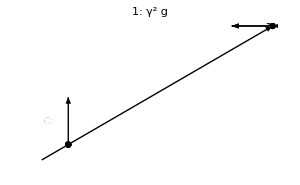
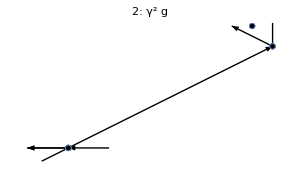
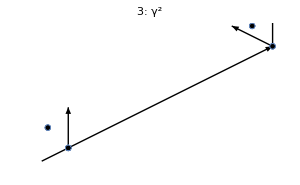
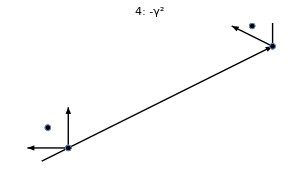
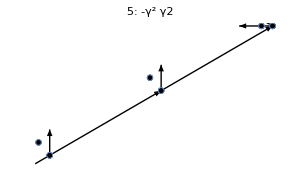
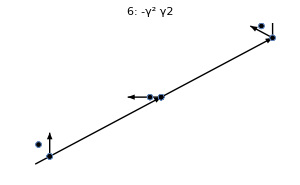

```mathematica
DrawFromContraction[(OneLoopBackbone),"print"->False,"showEndLines"->True,"ImageSize"->300]
```

### OneLoop: contraction form OneLoopBackbone

```mathematica
SpreadInteractions[nInteractionVertices,"endTime"->(endTime+1),"Vγ2δ"->True]
```

V[-g χ[x_11,i_65104,α_65104,t_3] χs[x_11,i_65104,α_65104,t_3] ψ[x_11,t_3]]+V[-g χ[x_21,i_91095,α_91095,t_2] χs[x_21,i_91095,α_91095,t_2] ψ[x_21,t_2]]+V[-g χ[x_31,i_55474,α_55474,t_1] χs[x_31,i_55474,α_55474,t_1] ψ[x_31,t_1]]

```mathematica
nInteractionVertices=2;
nγ2=0;
nγ2Minus=0;
endTime=nInteractionVertices+nγ2+nγ2Minus+1;

(List@@(Plus@@Expand[(OneLoopBackbone*(SpreadInteractions[nInteractionVertices,"endTime"->(endTime+1),"Vγ2δ"->True])*(*Vψχ[Subscript[x,endTime+100],endTime+1]*)δχs[Subscript[x, endTime+1],1,2,Subscript[t, endTime+1]])])
);


AbsoluteTiming[OneLoop=Plus@@(WickContractionSpaceVerticesMODfaster[#, "endTime"->(endTime+1),"print"->False,"fields"->FieldsNamesGenerator[{χ,ψ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True,"maxContractions"->100]&/@%)/.ψs[__]->0]
```

{5.90453,-g^2 γ^2 ϕs[x_2,t_3] χs[x_1,1,2,t_4] χs[x_2,1,2,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_4,t_4] G_χ[x_2,x_2,t_2] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4]-g^2 γ^2 γ2 DD[G_χ[x_2,x_3,t_3]] ϕs[x_3,t_4] χs[x_1,1,2,t_4] χs[x_2,1,2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3]-g^2 γ^2 ϕs[x_2,t_3] χs[x_1,1,2,t_1] χs[x_2,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_1,t_1] G_χ[x_2,x_4,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]-g^2 γ^2 γ2 DD[G_χ[x_1,x_3,t_3]] ϕs[x_3,t_4] χs[x_1,1,2,t_3] χs[x_2,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_2,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]+g^2 γ^2 ϕs[x_2,t_3] χs[x_2,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_4,t_4] G_χ[x_2,x_1,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]+g^2 γ^2 ϕs[x_2,t_3] χs[x_1,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_2,t_4] G_χ[x_2,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]-g^2 γ^2 γ2 DD[G_χ[x_1,x_2,t_2]] ϕs[x_3,t_4] χs[x_1,1,2,t_2] χs[x_3,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_3,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_3,x_3,t_4]}

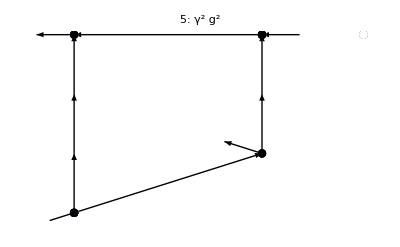
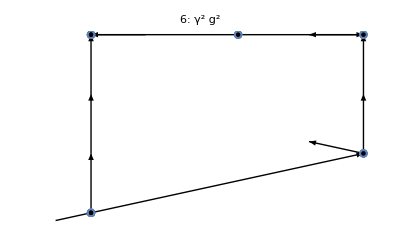
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
OneLoop/.Subscript[G, χ][Subscript[x, a_],Subscript[x, 4],Subscript[t, 4]]:>χ[Subscript[x, a],Subscript[t, 4]];
DrawFromContraction[%,"print"->False,"showEndLines"->True,"ImageSize"->Scaled[0.3]]
```

```mathematica
(* This looks ok, let's see 2-Loop*)
```

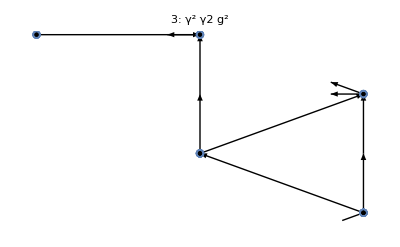
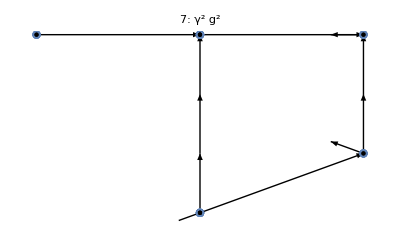
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
DDeatsG[OneLoop];
DrawFromContraction[%,"print"->False,"showEndLines"->True,"ImageSize"->Scaled[0.3]]
```

## 2-Loop:

### TwoLoopBackbone

#### Generate TwoLoopγList

```mathematica
nInteractionVertices=2;
nγ2=0;
nγ2Minus=0;
endTime=nInteractionVertices+nInteractionVertices+1;

TwoLoopγList=((*V[ϕs[Subscript[x, 0],Subscript[t, 1]]]**)Flatten[(Table[Table[Table[Spreadγ[nInteractionVertices+1,"print"->False,"nγ1δ"->(kkk-jjj),"nγ2"->iii,"nγ2Minus"->(jjj-iii),"evaluate"->False],
{iii,0,jjj}],
{jjj,0,(kkk)}],
{kkk,0,(nInteractionVertices)}])
,3]
)
```

{{Vγ1,Vγ1,Vγ1δ},{Vγ1,Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ1,Vγ1,Vγ2},{Vγ1,Vγ1δ,Vγ1δ},{Vγ1,Vγ1,Vγ1δ,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,Vγ1δ},{Vγ1,Vγ1δ,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1,Vγ1δ},{Vγ1,Vγ1,Vγ1δ,Vγ2},{Vγ1,Vγ1,Vγ2,Vγ1δ},{Vγ1,Vγ1δ,Vγ1,Vγ2},{Vγ1,Vγ2,Vγ1,Vγ1δ},{Vγ1,Vγ1,Vγ1,Vγ2Minus,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ1,Vγ1,Vγ2,Vγ2Minus},{Vγ1,Vγ1,Vγ1,Vγ2Minus,Vγ2},{Vγ1,Vγ1,Vγ2,Vγ1,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,Vγ1,Vγ2},{Vγ1,Vγ2,Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1,Vγ1,Vγ2},{Vγ1,Vγ1,Vγ1,Vγ2,Vγ2},{Vγ1,Vγ1,Vγ2,Vγ1,Vγ2},{Vγ1,Vγ2,Vγ1,Vγ1,Vγ2}}

#### Apply Lastγ2pCancelsLastγ2m (Rule 1) to TwoLoopγList -> TwoLoopγListRule1

```mathematica
TwoLoopγListRule1=Lastγ2pCancelsLastγ2m[TwoLoopγList]
```

{{Vγ1,Vγ1,Vγ1δ},{Vγ1,Vγ1δ,Vγ1δ},{Vγ1,Vγ1,Vγ2Minus,Vγ1δ},{Vγ1,Vγ2Minus,Vγ1,Vγ1δ},{Vγ1,Vγ1,Vγ2,Vγ1δ},{Vγ1,Vγ2,Vγ1,Vγ1δ}}

#### Apply γ1FollowedByγ2p (Rule 2) to TwoLoopγListRule1 -> TwoLoopγListRule2

```mathematica
TwoLoopγListRule2=γ1FollowedByγ2p[TwoLoopγListRule1]
```

{{Vγ1,Vγ1,Vγ1δ},{Vγ1,Vγ1δ,Vγ1δ},{Vγ1,Vγ1,Vγ2Minus,Vγ1δ},{Vγ1,Vγ2Minus,Vγ1,Vγ1δ},{Vγ1,-Vγ1δ,Vγ1δ},{Vγ1,Vγg,Vγ1δ},{-Vγ1δ,Vγ1,Vγ1δ},{Vγg,Vγ1,Vγ1δ}}

#### Evaluate the vertices in TwoLoopγListRule2 -> TwoLoopγListEvaluated

```mathematica
TwoLoopγListEvaluated=EvaluateVertices[TwoLoopγListRule2]
```

{V[ϕs[x_0,t_1]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ δχs[x_3,1,2,t_3] ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],V[ϕs[x_0,t_1]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ δχs[x_2,1,2,t_2] ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ δχs[x_3,1,2,t_3] ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_3,1,2,t_3]] ϕ[x_3,t_3] ϕs[x_3,t_4]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ δχs[x_4,1,2,t_4] ϕ[x_4,t_4] ϕs[x_4,t_5] ψs[x_4,t_5]],V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_2,1,2,t_2]] ϕ[x_2,t_2] ϕs[x_2,t_3]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]] V[γ δχs[x_4,1,2,t_4] ϕ[x_4,t_4] ϕs[x_4,t_5] ψs[x_4,t_5]],V[ϕs[x_0,t_1]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ δχs[x_3,1,2,t_3] ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]] (-Vγ1δ)[x_2,2],V[ϕs[x_0,t_1]] V[g γ δχs[x_2,1,2,t_2] ϕ[x_2,t_2] ϕs[x_2,t_3] χ[x_2,1,2,t_2] χs[x_2,1,2,t_2]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ δχs[x_3,1,2,t_3] ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],V[ϕs[x_0,t_1]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ δχs[x_3,1,2,t_3] ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]] (-Vγ1δ)[x_1,1],V[ϕs[x_0,t_1]] V[g γ δχs[x_1,1,2,t_1] ϕ[x_1,t_1] ϕs[x_1,t_2] χ[x_1,1,2,t_1] χs[x_1,1,2,t_1]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ δχs[x_3,1,2,t_3] ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]]}

#### Contract ϕ in TwoLoopγListEvaluated -> TwoLoopBackbone

```mathematica
List@@(Plus@@TwoLoopγListEvaluated);

AbsoluteTiming[TwoLoopBackbone=List@@(Plus@@(WickContractionSpaceVerticesMODfaster[#,"fields"->FieldsNamesGenerator[{ϕ}], "endTime"->(endTime+1),"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->False,"FreeAction"->NONE,"maxContractions"->100]&/@%))]
```

{0.0301153,{g γ^3 δχs[x_2,1,2,t_2] δχs[x_3,1,2,t_3] ϕs[x_3,t_4] χ[x_2,1,2,t_2] χs[x_2,1,2,t_2] ψs[x_1,t_2] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],g γ^3 δχs[x_1,1,2,t_1] δχs[x_3,1,2,t_3] ϕs[x_3,t_4] χ[x_1,1,2,t_1] χs[x_1,1,2,t_1] ψs[x_2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],γ^3 δχs[x_3,1,2,t_3] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],γ^3 δχs[x_2,1,2,t_2] δχs[x_3,1,2,t_3] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],-γ^3 γ2 DD[δχs[x_3,1,2,t_3]] δχs[x_4,1,2,t_4] ϕs[x_4,t_5] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4],-γ^3 γ2 DD[δχs[x_2,1,2,t_2]] δχs[x_4,1,2,t_4] ϕs[x_4,t_5] ψs[x_1,t_2] ψs[x_3,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4]}}

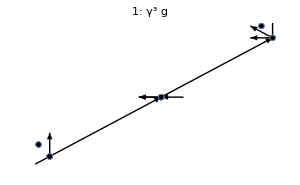
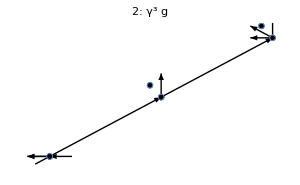
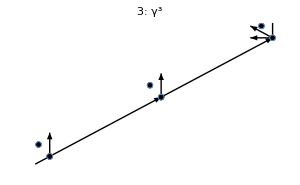
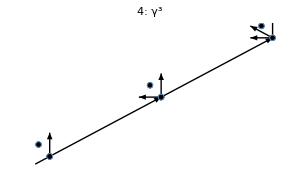
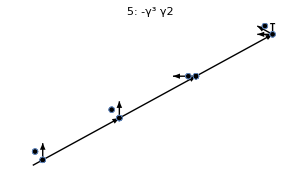
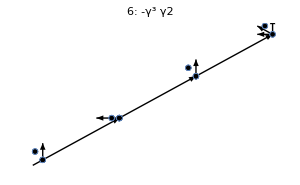

```mathematica
DrawFromContraction[(TwoLoopBackbone),"print"->False,"showEndLines"->True,"ImageSize"->300]
```

#### Tree exclusion (by eye) as well as elemination of δχ in first position -> TwoLoopBackboneSimplified

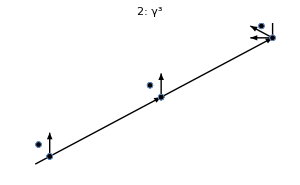
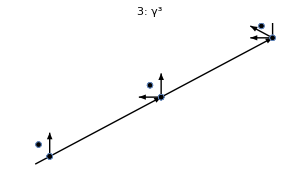
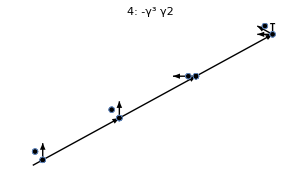
-Graphics--Graphics--Graphics--Graphics-

```mathematica
TwoLoopBackboneSimplified=Delete[TwoLoopBackbone,{{2},{6}}];
DrawFromContraction[(TwoLoopBackboneSimplified),"print"->False,"showEndLines"->True,"ImageSize"->300]
```

### TwoLoop: contraction form TwoLoopBackboneSimplified

#### Give interaction vertices to TwoLoopBackboneSimplified with GiveInteractionVertices[] -> TwoLoopBackboneWithInteractions

```mathematica
nInteractionVertices=2;
TwoLoopBackboneWithInteractions=GiveInteractionVertices[TwoLoopBackboneSimplified,"nInteractions"->nInteractionVertices]
```

{g γ^3 V[-g χ[x_11,i_75506,α_75506,t_3] χs[x_11,i_75506,α_75506,t_3] ψ[x_11,t_3]] δχs[x_2,1,2,t_2] δχs[x_3,1,2,t_3] ϕs[x_3,t_4] χ[x_2,1,2,t_2] χs[x_2,1,2,t_2] ψs[x_1,t_2] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],g γ^3 V[-g χ[x_21,i_77828,α_77828,t_2] χs[x_21,i_77828,α_77828,t_2] ψ[x_21,t_2]] δχs[x_2,1,2,t_2] δχs[x_3,1,2,t_3] ϕs[x_3,t_4] χ[x_2,1,2,t_2] χs[x_2,1,2,t_2] ψs[x_1,t_2] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],g γ^3 V[-g χ[x_31,i_86990,α_86990,t_1] χs[x_31,i_86990,α_86990,t_1] ψ[x_31,t_1]] δχs[x_2,1,2,t_2] δχs[x_3,1,2,t_3] ϕs[x_3,t_4] χ[x_2,1,2,t_2] χs[x_2,1,2,t_2] ψs[x_1,t_2] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],γ^3 V[-g χ[x_11,i_26780,α_26780,t_3] χs[x_11,i_26780,α_26780,t_3] ψ[x_11,t_3]] V[-g χ[x_12,i_5624,α_5624,t_3] χs[x_12,i_5624,α_5624,t_3] ψ[x_12,t_3]] δχs[x_3,1,2,t_3] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],γ^3 V[-g χ[x_11,i_89393,α_89393,t_3] χs[x_11,i_89393,α_89393,t_3] ψ[x_11,t_3]] V[-g χ[x_21,i_96587,α_96587,t_2] χs[x_21,i_96587,α_96587,t_2] ψ[x_21,t_2]] δχs[x_3,1,2,t_3] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],γ^3 V[-g χ[x_21,i_92058,α_92058,t_2] χs[x_21,i_92058,α_92058,t_2] ψ[x_21,t_2]] V[-g χ[x_22,i_63604,α_63604,t_2] χs[x_22,i_63604,α_63604,t_2] ψ[x_22,t_2]] δχs[x_3,1,2,t_3] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],γ^3 V[-g χ[x_21,i_10324,α_10324,t_2] χs[x_21,i_10324,α_10324,t_2] ψ[x_21,t_2]] V[-g χ[x_31,i_13440,α_13440,t_1] χs[x_31,i_13440,α_13440,t_1] ψ[x_31,t_1]] δχs[x_3,1,2,t_3] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],γ^3 V[-g χ[x_11,i_28667,α_28667,t_3] χs[x_11,i_28667,α_28667,t_3] ψ[x_11,t_3]] V[-g χ[x_31,i_57072,α_57072,t_1] χs[x_31,i_57072,α_57072,t_1] ψ[x_31,t_1]] δχs[x_3,1,2,t_3] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],γ^3 V[-g χ[x_31,i_57143,α_57143,t_1] χs[x_31,i_57143,α_57143,t_1] ψ[x_31,t_1]] V[-g χ[x_32,i_66731,α_66731,t_1] χs[x_32,i_66731,α_66731,t_1] ψ[x_32,t_1]] δχs[x_3,1,2,t_3] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],γ^3 V[-g χ[x_11,i_88067,α_88067,t_3] χs[x_11,i_88067,α_88067,t_3] ψ[x_11,t_3]] V[-g χ[x_12,i_54569,α_54569,t_3] χs[x_12,i_54569,α_54569,t_3] ψ[x_12,t_3]] δχs[x_2,1,2,t_2] δχs[x_3,1,2,t_3] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],γ^3 V[-g χ[x_11,i_53932,α_53932,t_3] χs[x_11,i_53932,α_53932,t_3] ψ[x_11,t_3]] V[-g χ[x_21,i_93062,α_93062,t_2] χs[x_21,i_93062,α_93062,t_2] ψ[x_21,t_2]] δχs[x_2,1,2,t_2] δχs[x_3,1,2,t_3] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],γ^3 V[-g χ[x_21,i_53918,α_53918,t_2] χs[x_21,i_53918,α_53918,t_2] ψ[x_21,t_2]] V[-g χ[x_22,i_82346,α_82346,t_2] χs[x_22,i_82346,α_82346,t_2] ψ[x_22,t_2]] δχs[x_2,1,2,t_2] δχs[x_3,1,2,t_3] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],γ^3 V[-g χ[x_21,i_95419,α_95419,t_2] χs[x_21,i_95419,α_95419,t_2] ψ[x_21,t_2]] V[-g χ[x_31,i_46747,α_46747,t_1] χs[x_31,i_46747,α_46747,t_1] ψ[x_31,t_1]] δχs[x_2,1,2,t_2] δχs[x_3,1,2,t_3] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],γ^3 V[-g χ[x_11,i_78724,α_78724,t_3] χs[x_11,i_78724,α_78724,t_3] ψ[x_11,t_3]] V[-g χ[x_31,i_78481,α_78481,t_1] χs[x_31,i_78481,α_78481,t_1] ψ[x_31,t_1]] δχs[x_2,1,2,t_2] δχs[x_3,1,2,t_3] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],γ^3 V[-g χ[x_31,i_85033,α_85033,t_1] χs[x_31,i_85033,α_85033,t_1] ψ[x_31,t_1]] V[-g χ[x_32,i_9251,α_9251,t_1] χs[x_32,i_9251,α_9251,t_1] ψ[x_32,t_1]] δχs[x_2,1,2,t_2] δχs[x_3,1,2,t_3] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],-γ^3 γ2 DD[δχs[x_3,1,2,t_3]] V[-g χ[x_11,i_25574,α_25574,t_4] χs[x_11,i_25574,α_25574,t_4] ψ[x_11,t_4]] V[-g χ[x_12,i_7408,α_7408,t_4] χs[x_12,i_7408,α_7408,t_4] ψ[x_12,t_4]] δχs[x_4,1,2,t_4] ϕs[x_4,t_5] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4],-γ^3 γ2 DD[δχs[x_3,1,2,t_3]] V[-g χ[x_11,i_20878,α_20878,t_4] χs[x_11,i_20878,α_20878,t_4] ψ[x_11,t_4]] V[-g χ[x_21,i_85878,α_85878,t_3] χs[x_21,i_85878,α_85878,t_3] ψ[x_21,t_3]] δχs[x_4,1,2,t_4] ϕs[x_4,t_5] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4],-γ^3 γ2 DD[δχs[x_3,1,2,t_3]] V[-g χ[x_21,i_33205,α_33205,t_3] χs[x_21,i_33205,α_33205,t_3] ψ[x_21,t_3]] V[-g χ[x_22,i_80858,α_80858,t_3] χs[x_22,i_80858,α_80858,t_3] ψ[x_22,t_3]] δχs[x_4,1,2,t_4] ϕs[x_4,t_5] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4],-γ^3 γ2 DD[δχs[x_3,1,2,t_3]] V[-g χ[x_21,i_64631,α_64631,t_3] χs[x_21,i_64631,α_64631,t_3] ψ[x_21,t_3]] V[-g χ[x_31,i_3593,α_3593,t_2] χs[x_31,i_3593,α_3593,t_2] ψ[x_31,t_2]] δχs[x_4,1,2,t_4] ϕs[x_4,t_5] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4],-γ^3 γ2 DD[δχs[x_3,1,2,t_3]] V[-g χ[x_11,i_64073,α_64073,t_4] χs[x_11,i_64073,α_64073,t_4] ψ[x_11,t_4]] V[-g χ[x_31,i_66866,α_66866,t_2] χs[x_31,i_66866,α_66866,t_2] ψ[x_31,t_2]] δχs[x_4,1,2,t_4] ϕs[x_4,t_5] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4],-γ^3 γ2 DD[δχs[x_3,1,2,t_3]] V[-g χ[x_31,i_85166,α_85166,t_2] χs[x_31,i_85166,α_85166,t_2] ψ[x_31,t_2]] V[-g χ[x_32,i_29268,α_29268,t_2] χs[x_32,i_29268,α_29268,t_2] ψ[x_32,t_2]] δχs[x_4,1,2,t_4] ϕs[x_4,t_5] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4],-γ^3 γ2 DD[δχs[x_3,1,2,t_3]] V[-g χ[x_31,i_24816,α_24816,t_2] χs[x_31,i_24816,α_24816,t_2] ψ[x_31,t_2]] V[-g χ[x_41,i_95372,α_95372,t_1] χs[x_41,i_95372,α_95372,t_1] ψ[x_41,t_1]] δχs[x_4,1,2,t_4] ϕs[x_4,t_5] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4],-γ^3 γ2 DD[δχs[x_3,1,2,t_3]] V[-g χ[x_21,i_30683,α_30683,t_3] χs[x_21,i_30683,α_30683,t_3] ψ[x_21,t_3]] V[-g χ[x_41,i_96540,α_96540,t_1] χs[x_41,i_96540,α_96540,t_1] ψ[x_41,t_1]] δχs[x_4,1,2,t_4] ϕs[x_4,t_5] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4],-γ^3 γ2 DD[δχs[x_3,1,2,t_3]] V[-g χ[x_11,i_86816,α_86816,t_4] χs[x_11,i_86816,α_86816,t_4] ψ[x_11,t_4]] V[-g χ[x_41,i_97631,α_97631,t_1] χs[x_41,i_97631,α_97631,t_1] ψ[x_41,t_1]] δχs[x_4,1,2,t_4] ϕs[x_4,t_5] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4],-γ^3 γ2 DD[δχs[x_3,1,2,t_3]] V[-g χ[x_41,i_63592,α_63592,t_1] χs[x_41,i_63592,α_63592,t_1] ψ[x_41,t_1]] V[-g χ[x_42,i_23003,α_23003,t_1] χs[x_42,i_23003,α_23003,t_1] ψ[x_42,t_1]] δχs[x_4,1,2,t_4] ϕs[x_4,t_5] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4]}

#### Perform the contraction on TwoLoopBackboneWithInteractions -> TwoLoop

```mathematica
TwoLoopBackboneWithInteractions;

AbsoluteTiming[

TwoLoop=Module[{exprToContract,contracted},

exprToContract=TwoLoopBackboneWithInteractions;

contracted=Plus@@(WickContractionSpaceVerticesMODfaster[#, "endTime"->(Cases[#,ϕs[_,Subscript[t,k_]]:>k,All][[1]]-1),"print"->False,"fields"->FieldsNamesGenerator[{χ,ψ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True,"maxContractions"->100]&/@exprToContract);

contracted
];
]
```

{8.92162,Null}

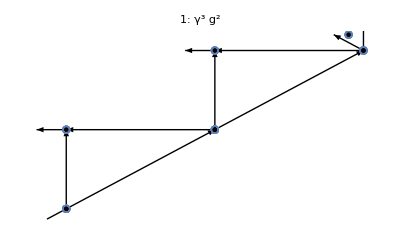
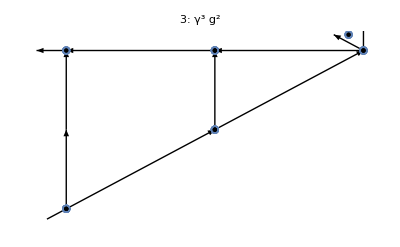
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
DrawFromContraction[TwoLoop/.δχs[__]->0,"print"->False,"showEndLines"->True,"ImageSize"->Scaled[0.33]]
```

### TwoLoopBackboneBIS: WITH RULE 2 DONE BEFORE RULE 1

#### Generate TwoLoopγList

```mathematica
nInteractionVertices=2;
nγ2=0;
nγ2Minus=0;
endTime=nInteractionVertices+nInteractionVertices+1;

TwoLoopγList=((*V[ϕs[Subscript[x, 0],Subscript[t, 1]]]**)Flatten[(Table[Table[Table[Spreadγ[nInteractionVertices+1,"print"->False,"nγ1δ"->(kkk-jjj),"nγ2"->iii,"nγ2Minus"->(jjj-iii),"evaluate"->False],
{iii,0,jjj}],
{jjj,0,(kkk)}],
{kkk,0,(nInteractionVertices)}])
,3]
)
```

{{Vγ1,Vγ1,Vγ1δ},{Vγ1,Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ1,Vγ1,Vγ2},{Vγ1,Vγ1δ,Vγ1δ},{Vγ1,Vγ1,Vγ1δ,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,Vγ1δ},{Vγ1,Vγ1δ,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1,Vγ1δ},{Vγ1,Vγ1,Vγ1δ,Vγ2},{Vγ1,Vγ1,Vγ2,Vγ1δ},{Vγ1,Vγ1δ,Vγ1,Vγ2},{Vγ1,Vγ2,Vγ1,Vγ1δ},{Vγ1,Vγ1,Vγ1,Vγ2Minus,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ1,Vγ1,Vγ2,Vγ2Minus},{Vγ1,Vγ1,Vγ1,Vγ2Minus,Vγ2},{Vγ1,Vγ1,Vγ2,Vγ1,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,Vγ1,Vγ2},{Vγ1,Vγ2,Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1,Vγ1,Vγ2},{Vγ1,Vγ1,Vγ1,Vγ2,Vγ2},{Vγ1,Vγ1,Vγ2,Vγ1,Vγ2},{Vγ1,Vγ2,Vγ1,Vγ1,Vγ2}}

#### Apply γ1FollowedByγ2p (Rule 2) to TwoLoopγList -> TwoLoopγListRule2

```mathematica
TwoLoopγListRule2=γ1FollowedByγ2p[TwoLoopγList]
```

{{Vγ1,Vγ1,Vγ1δ},{Vγ1,Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ1,-Vγ1δ},{Vγ1,Vγ1,Vγg},{Vγ1,Vγ1δ,Vγ1δ},{Vγ1,Vγ1,Vγ1δ,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,Vγ1δ},{Vγ1,Vγ1δ,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1,Vγ1δ},{Vγ1,Vγ1,Vγ1δ,Vγ2},{Vγ1,-Vγ1δ,Vγ1δ},{Vγ1,Vγg,Vγ1δ},{Vγ1,Vγ1δ,-Vγ1δ},{Vγ1,Vγ1δ,Vγg},{-Vγ1δ,Vγ1,Vγ1δ},{Vγg,Vγ1,Vγ1δ},{Vγ1,Vγ1,Vγ1,Vγ2Minus,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ1,-Vγ1δ,Vγ2Minus},{Vγ1,Vγ1,Vγg,Vγ2Minus},{Vγ1,Vγ1,Vγ1,Vγ2Minus,Vγ2},{Vγ1,-Vγ1δ,Vγ1,Vγ2Minus},{Vγ1,Vγg,Vγ1,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,-Vγ1δ},{Vγ1,Vγ1,Vγ2Minus,Vγg},{-Vγ1δ,Vγ1,Vγ1,Vγ2Minus},{Vγg,Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1,-Vγ1δ},{Vγ1,Vγ2Minus,Vγ1,Vγg},{Vγ1,Vγ1,-Vγ1δ,Vγ2},{Vγ1,Vγ1,Vγg,Vγ2},{Vγ1,-Vγ1δ,Vγ1,Vγ2},{Vγ1,Vγg,Vγ1,Vγ2},{-Vγ1δ,Vγ1,Vγ1,Vγ2},{Vγg,Vγ1,Vγ1,Vγ2}}

#### Apply Lastγ2pCancelsLastγ2m (Rule 1) to TwoLoopγListRule2 -> TwoLoopγListRule1

TRY SKIPPING THIS:

```mathematica
TwoLoopγListRule1=Lastγ2pCancelsLastγ2m[TwoLoopγListRule2]
```

{{Vγ1,Vγ1,Vγ1δ},{Vγ1,Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ1,-Vγ1δ},{Vγ1,Vγ1,Vγg},{Vγ1,Vγ1δ,Vγ1δ},{Vγ1,Vγ1,Vγ2Minus,Vγ1δ},{Vγ1,Vγ1δ,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1,Vγ1δ},{Vγ1,-Vγ1δ,Vγ1δ},{Vγ1,Vγg,Vγ1δ},{Vγ1,Vγ1δ,-Vγ1δ},{Vγ1,Vγ1δ,Vγg},{-Vγ1δ,Vγ1,Vγ1δ},{Vγg,Vγ1,Vγ1δ},{Vγ1,Vγ1,Vγ2Minus,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,-Vγ1δ},{Vγ1,Vγ1,Vγ2Minus,Vγg},{Vγ1,Vγ2Minus,Vγ1,-Vγ1δ},{Vγ1,Vγ2Minus,Vγ1,Vγg}}

THAT IS:

```mathematica
TwoLoopγListRule1=TwoLoopγListRule2
```

{{Vγ1,Vγ1,Vγ1δ},{Vγ1,Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ1,-Vγ1δ},{Vγ1,Vγ1,Vγg},{Vγ1,Vγ1δ,Vγ1δ},{Vγ1,Vγ1,Vγ1δ,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,Vγ1δ},{Vγ1,Vγ1δ,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1,Vγ1δ},{Vγ1,Vγ1,Vγ1δ,Vγ2},{Vγ1,-Vγ1δ,Vγ1δ},{Vγ1,Vγg,Vγ1δ},{Vγ1,Vγ1δ,-Vγ1δ},{Vγ1,Vγ1δ,Vγg},{-Vγ1δ,Vγ1,Vγ1δ},{Vγg,Vγ1,Vγ1δ},{Vγ1,Vγ1,Vγ1,Vγ2Minus,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ1,-Vγ1δ,Vγ2Minus},{Vγ1,Vγ1,Vγg,Vγ2Minus},{Vγ1,Vγ1,Vγ1,Vγ2Minus,Vγ2},{Vγ1,-Vγ1δ,Vγ1,Vγ2Minus},{Vγ1,Vγg,Vγ1,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,-Vγ1δ},{Vγ1,Vγ1,Vγ2Minus,Vγg},{-Vγ1δ,Vγ1,Vγ1,Vγ2Minus},{Vγg,Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1,-Vγ1δ},{Vγ1,Vγ2Minus,Vγ1,Vγg},{Vγ1,Vγ1,-Vγ1δ,Vγ2},{Vγ1,Vγ1,Vγg,Vγ2},{Vγ1,-Vγ1δ,Vγ1,Vγ2},{Vγ1,Vγg,Vγ1,Vγ2},{-Vγ1δ,Vγ1,Vγ1,Vγ2},{Vγg,Vγ1,Vγ1,Vγ2}}

#### Evaluate the vertices in TwoLoopγListRule1 -> TwoLoopγListEvaluatedBIS

```mathematica
TwoLoopγListEvaluatedBIS=EvaluateVertices[TwoLoopγListRule1]
```

{V[ϕs[x_0,t_1]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ δχs[x_3,1,2,t_3] ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_4,1,2,t_4]] ϕ[x_4,t_4] ϕs[x_4,t_5]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],-V[ϕs[x_0,t_1]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ δχs[x_3,1,2,t_3] ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],V[ϕs[x_0,t_1]] V[g γ δχs[x_3,1,2,t_3] ϕ[x_3,t_3] ϕs[x_3,t_4] χ[x_3,i_13625,α_13625,t_3] χs[x_3,i_13625,α_13625,t_3]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ δχs[x_2,1,2,t_2] ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ δχs[x_3,1,2,t_3] ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_4,1,2,t_4]] ϕ[x_4,t_4] ϕs[x_4,t_5]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ δχs[x_3,1,2,t_3] ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_3,1,2,t_3]] ϕ[x_3,t_3] ϕs[x_3,t_4]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ δχs[x_4,1,2,t_4] ϕ[x_4,t_4] ϕs[x_4,t_5] ψs[x_4,t_5]],V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_4,1,2,t_4]] ϕ[x_4,t_4] ϕs[x_4,t_5]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ δχs[x_2,1,2,t_2] ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_2,1,2,t_2]] ϕ[x_2,t_2] ϕs[x_2,t_3]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]] V[γ δχs[x_4,1,2,t_4] ϕ[x_4,t_4] ϕs[x_4,t_5] ψs[x_4,t_5]],V[ϕs[x_0,t_1]] V[γ2 DD[ϕ[x_4,t_4]] δχs[x_4,1,2,t_4] ϕs[x_4,t_5]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ δχs[x_3,1,2,t_3] ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],-V[ϕs[x_0,t_1]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ δχs[x_2,1,2,t_2] ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ δχs[x_3,1,2,t_3] ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],V[ϕs[x_0,t_1]] V[g γ δχs[x_2,1,2,t_2] ϕ[x_2,t_2] ϕs[x_2,t_3] χ[x_2,i_100,α_100,t_2] χs[x_2,i_100,α_100,t_2]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ δχs[x_3,1,2,t_3] ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],-V[ϕs[x_0,t_1]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ δχs[x_2,1,2,t_2] ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ δχs[x_3,1,2,t_3] ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],V[ϕs[x_0,t_1]] V[g γ δχs[x_3,1,2,t_3] ϕ[x_3,t_3] ϕs[x_3,t_4] χ[x_3,i_31263,α_31263,t_3] χs[x_3,i_31263,α_31263,t_3]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ δχs[x_2,1,2,t_2] ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],-V[ϕs[x_0,t_1]] V[γ δχs[x_1,1,2,t_1] ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ δχs[x_3,1,2,t_3] ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],V[ϕs[x_0,t_1]] V[g γ δχs[x_1,1,2,t_1] ϕ[x_1,t_1] ϕs[x_1,t_2] χ[x_1,i_14870,α_14870,t_1] χs[x_1,i_14870,α_14870,t_1]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ δχs[x_3,1,2,t_3] ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_4,1,2,t_4]] ϕ[x_4,t_4] ϕs[x_4,t_5]] V[-γ2 DD[δχs[x_5,1,2,t_5]] ϕ[x_5,t_5] ϕs[x_5,t_6]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_3,1,2,t_3]] ϕ[x_3,t_3] ϕs[x_3,t_4]] V[-γ2 DD[δχs[x_5,1,2,t_5]] ϕ[x_5,t_5] ϕs[x_5,t_6]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ ϕ[x_4,t_4] ϕs[x_4,t_5] ψs[x_4,t_5]],V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_2,1,2,t_2]] ϕ[x_2,t_2] ϕs[x_2,t_3]] V[-γ2 DD[δχs[x_5,1,2,t_5]] ϕ[x_5,t_5] ϕs[x_5,t_6]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]] V[γ ϕ[x_4,t_4] ϕs[x_4,t_5] ψs[x_4,t_5]],-V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_4,1,2,t_4]] ϕ[x_4,t_4] ϕs[x_4,t_5]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ δχs[x_3,1,2,t_3] ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_4,1,2,t_4]] ϕ[x_4,t_4] ϕs[x_4,t_5]] V[g γ δχs[x_3,1,2,t_3] ϕ[x_3,t_3] ϕs[x_3,t_4] χ[x_3,i_19720,α_19720,t_3] χs[x_3,i_19720,α_19720,t_3]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_4,1,2,t_4]] ϕ[x_4,t_4] ϕs[x_4,t_5]] V[γ2 DD[ϕ[x_5,t_5]] δχs[x_5,1,2,t_5] ϕs[x_5,t_6]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],-V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_4,1,2,t_4]] ϕ[x_4,t_4] ϕs[x_4,t_5]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ δχs[x_2,1,2,t_2] ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_4,1,2,t_4]] ϕ[x_4,t_4] ϕs[x_4,t_5]] V[g γ δχs[x_2,1,2,t_2] ϕ[x_2,t_2] ϕs[x_2,t_3] χ[x_2,i_51082,α_51082,t_2] χs[x_2,i_51082,α_51082,t_2]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],-V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_3,1,2,t_3]] ϕ[x_3,t_3] ϕs[x_3,t_4]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ δχs[x_4,1,2,t_4] ϕ[x_4,t_4] ϕs[x_4,t_5] ψs[x_4,t_5]],V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_3,1,2,t_3]] ϕ[x_3,t_3] ϕs[x_3,t_4]] V[g γ δχs[x_4,1,2,t_4] ϕ[x_4,t_4] ϕs[x_4,t_5] χ[x_4,i_95644,α_95644,t_4] χs[x_4,i_95644,α_95644,t_4]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],-V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_4,1,2,t_4]] ϕ[x_4,t_4] ϕs[x_4,t_5]] V[γ δχs[x_1,1,2,t_1] ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_4,1,2,t_4]] ϕ[x_4,t_4] ϕs[x_4,t_5]] V[g γ δχs[x_1,1,2,t_1] ϕ[x_1,t_1] ϕs[x_1,t_2] χ[x_1,i_40830,α_40830,t_1] χs[x_1,i_40830,α_40830,t_1]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],-V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_2,1,2,t_2]] ϕ[x_2,t_2] ϕs[x_2,t_3]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]] V[γ δχs[x_4,1,2,t_4] ϕ[x_4,t_4] ϕs[x_4,t_5] ψs[x_4,t_5]],V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_2,1,2,t_2]] ϕ[x_2,t_2] ϕs[x_2,t_3]] V[g γ δχs[x_4,1,2,t_4] ϕ[x_4,t_4] ϕs[x_4,t_5] χ[x_4,i_79072,α_79072,t_4] χs[x_4,i_79072,α_79072,t_4]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],-V[ϕs[x_0,t_1]] V[γ2 DD[ϕ[x_4,t_4]] δχs[x_4,1,2,t_4] ϕs[x_4,t_5]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ δχs[x_3,1,2,t_3] ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],V[ϕs[x_0,t_1]] V[γ2 DD[ϕ[x_4,t_4]] δχs[x_4,1,2,t_4] ϕs[x_4,t_5]] V[g γ δχs[x_3,1,2,t_3] ϕ[x_3,t_3] ϕs[x_3,t_4] χ[x_3,i_63497,α_63497,t_3] χs[x_3,i_63497,α_63497,t_3]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],-V[ϕs[x_0,t_1]] V[γ2 DD[ϕ[x_4,t_4]] δχs[x_4,1,2,t_4] ϕs[x_4,t_5]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ δχs[x_2,1,2,t_2] ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],V[ϕs[x_0,t_1]] V[γ2 DD[ϕ[x_4,t_4]] δχs[x_4,1,2,t_4] ϕs[x_4,t_5]] V[g γ δχs[x_2,1,2,t_2] ϕ[x_2,t_2] ϕs[x_2,t_3] χ[x_2,i_58094,α_58094,t_2] χs[x_2,i_58094,α_58094,t_2]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],-V[ϕs[x_0,t_1]] V[γ2 DD[ϕ[x_4,t_4]] δχs[x_4,1,2,t_4] ϕs[x_4,t_5]] V[γ δχs[x_1,1,2,t_1] ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],V[ϕs[x_0,t_1]] V[γ2 DD[ϕ[x_4,t_4]] δχs[x_4,1,2,t_4] ϕs[x_4,t_5]] V[g γ δχs[x_1,1,2,t_1] ϕ[x_1,t_1] ϕs[x_1,t_2] χ[x_1,i_48994,α_48994,t_1] χs[x_1,i_48994,α_48994,t_1]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]] V[γ ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]]}

#### Contract ϕ in TwoLoopγListEvaluatedBIS -> TwoLoopBackboneBIS

```mathematica
List@@(Plus@@TwoLoopγListEvaluatedBIS);

AbsoluteTiming[TwoLoopBackboneBIS=List@@(Plus@@(WickContractionSpaceVerticesMODfaster[#,"fields"->FieldsNamesGenerator[{ϕ}], "endTime"->(endTime+1),"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->False,"FreeAction"->NONE,"maxContractions"->100]&/@%))]
```

{0.333397,{g γ^3 δχs[x_3,1,2,t_3] ϕs[x_3,t_4] χ[x_3,i_13625,α_13625,t_3] χs[x_3,i_13625,α_13625,t_3] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],g γ^3 δχs[x_2,1,2,t_2] δχs[x_3,1,2,t_3] ϕs[x_3,t_4] χ[x_3,i_31263,α_31263,t_3] χs[x_3,i_31263,α_31263,t_3] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],g γ^3 γ2 DD[G_ϕ[x_4,x_3,t_4]] δχs[x_3,1,2,t_3] δχs[x_4,1,2,t_4] ϕs[x_4,t_5] χ[x_3,i_63497,α_63497,t_3] χs[x_3,i_63497,α_63497,t_3] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],g γ^3 δχs[x_2,1,2,t_2] δχs[x_3,1,2,t_3] ϕs[x_3,t_4] χ[x_2,i_100,α_100,t_2] χs[x_2,i_100,α_100,t_2] ψs[x_1,t_2] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],g γ^3 γ2 DD[G_ϕ[x_4,x_3,t_4]] δχs[x_2,1,2,t_2] δχs[x_4,1,2,t_4] ϕs[x_4,t_5] χ[x_2,i_58094,α_58094,t_2] χs[x_2,i_58094,α_58094,t_2] ψs[x_1,t_2] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],g γ^3 δχs[x_1,1,2,t_1] δχs[x_3,1,2,t_3] ϕs[x_3,t_4] χ[x_1,i_14870,α_14870,t_1] χs[x_1,i_14870,α_14870,t_1] ψs[x_2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],g γ^3 γ2 DD[G_ϕ[x_4,x_3,t_4]] δχs[x_1,1,2,t_1] δχs[x_4,1,2,t_4] ϕs[x_4,t_5] χ[x_1,i_48994,α_48994,t_1] χs[x_1,i_48994,α_48994,t_1] ψs[x_2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],-γ^3 δχs[x_1,1,2,t_1] δχs[x_3,1,2,t_3] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],-γ^3 δχs[x_2,1,2,t_2] δχs[x_3,1,2,t_3] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],-γ^3 γ2 DD[G_ϕ[x_4,x_3,t_4]] δχs[x_1,1,2,t_1] δχs[x_4,1,2,t_4] ϕs[x_4,t_5] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],-γ^3 γ2 DD[G_ϕ[x_4,x_3,t_4]] δχs[x_2,1,2,t_2] δχs[x_4,1,2,t_4] ϕs[x_4,t_5] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],-g γ^3 γ2 DD[δχs[x_4,1,2,t_4]] δχs[x_3,1,2,t_3] ϕs[x_4,t_5] χ[x_3,i_19720,α_19720,t_3] χs[x_3,i_19720,α_19720,t_3] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4],-g γ^3 γ2 DD[δχs[x_3,1,2,t_3]] δχs[x_4,1,2,t_4] ϕs[x_4,t_5] χ[x_4,i_95644,α_95644,t_4] χs[x_4,i_95644,α_95644,t_4] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4],-g γ^3 γ2 DD[δχs[x_4,1,2,t_4]] δχs[x_2,1,2,t_2] ϕs[x_4,t_5] χ[x_2,i_51082,α_51082,t_2] χs[x_2,i_51082,α_51082,t_2] ψs[x_1,t_2] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4],-g γ^3 γ2 DD[δχs[x_2,1,2,t_2]] δχs[x_4,1,2,t_4] ϕs[x_4,t_5] χ[x_4,i_79072,α_79072,t_4] χs[x_4,i_79072,α_79072,t_4] ψs[x_1,t_2] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4],-g γ^3 γ2 DD[δχs[x_4,1,2,t_4]] δχs[x_1,1,2,t_1] ϕs[x_4,t_5] χ[x_1,i_40830,α_40830,t_1] χs[x_1,i_40830,α_40830,t_1] ψs[x_2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4],-γ^3 γ2 DD[δχs[x_4,1,2,t_4]] ϕs[x_4,t_5] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4],γ^3 γ2 DD[δχs[x_4,1,2,t_4]] δχs[x_1,1,2,t_1] ϕs[x_4,t_5] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4],-γ^3 γ2^2 DD[δχs[x_4,1,2,t_4]] DD[G_ϕ[x_5,x_4,t_5]] δχs[x_5,1,2,t_5] ϕs[x_5,t_6] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4],γ^3 γ2^2 DD[δχs[x_4,1,2,t_4]] DD[δχs[x_5,1,2,t_5]] ϕs[x_5,t_6] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_ϕ[x_5,x_4,t_5],γ^3 γ2^2 DD[δχs[x_3,1,2,t_3]] DD[δχs[x_5,1,2,t_5]] ϕs[x_5,t_6] ψs[x_1,t_2] ψs[x_2,t_3] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_ϕ[x_5,x_4,t_5],γ^3 γ2^2 DD[δχs[x_2,1,2,t_2]] DD[δχs[x_5,1,2,t_5]] ϕs[x_5,t_6] ψs[x_1,t_2] ψs[x_3,t_4] ψs[x_4,t_5] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_ϕ[x_4,x_3,t_4] G_ϕ[x_5,x_4,t_5]}}

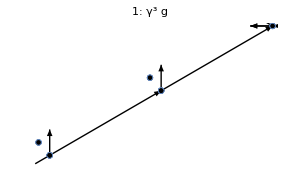
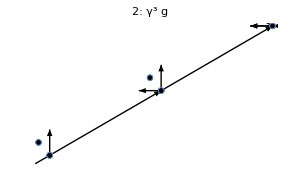
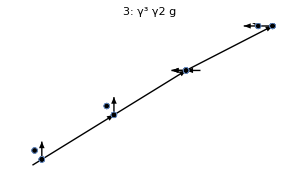
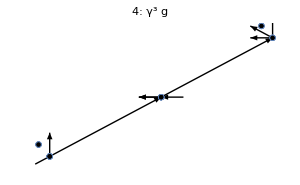
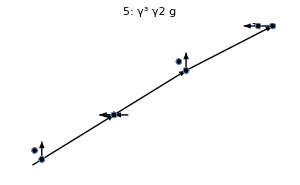
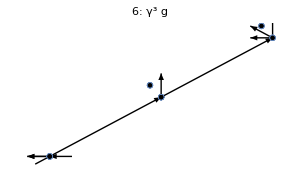
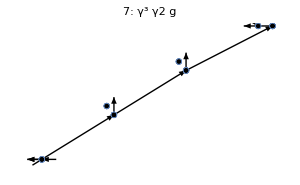
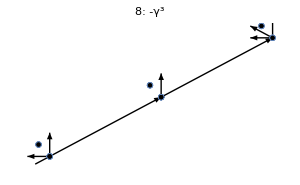

```mathematica
DrawFromContraction[(TwoLoopBackboneBIS),"print"->False,"showEndLines"->True,"ImageSize"->300]
```

#### Tree exclusion (by eye) as well as elemination of δχ in first position -> TwoLoopBackboneSimplifiedBIS

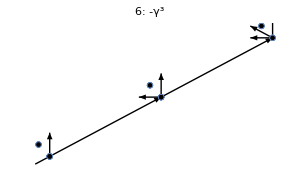
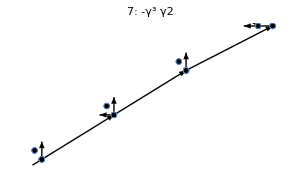
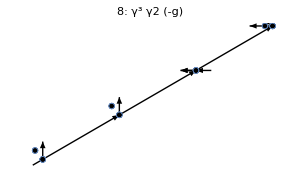
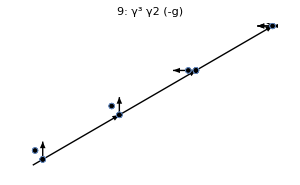
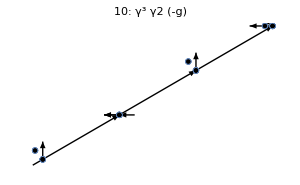
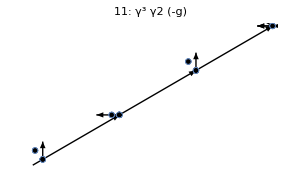
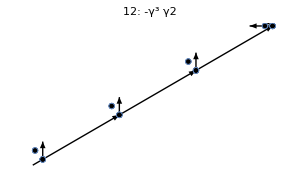
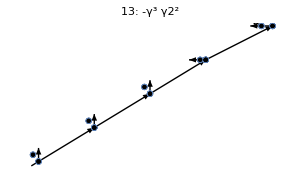
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
TwoLoopBackboneSimplifiedBIS=List@@(Plus@@TwoLoopBackboneBIS/.δχs[__,Subscript[t, 1]]:>0);
DrawFromContraction[(TwoLoopBackboneSimplifiedBIS),"print"->False,"showEndLines"->True,"ImageSize"->300]
```

### TwoLoopBIS: contraction form TwoLoopBackboneSimplifiedBIS

#### Give interaction vertices to TwoLoopBackboneSimplifiedBIS with GiveInteractionVertices[] -> TwoLoopBackboneWithInteractionsBIS

```mathematica
nInteractionVertices=2;
TwoLoopBackboneWithInteractionsBIS=GiveInteractionVertices[TwoLoopBackboneSimplifiedBIS,"nInteractions"->nInteractionVertices];
```

#### Perform the contraction on TwoLoopBackboneWithInteractionsBIS -> TwoLoopBIS

```mathematica
AbsoluteTiming[

TwoLoopBIS=Module[{exprToContract,contracted,i},

exprToContract=TwoLoopBackboneWithInteractionsBIS;

contracted=(Table[ WickContractionSpaceVerticesMODfaster[exprToContract[[i]], "endTime"->(Cases[exprToContract[[i]],ϕs[_,Subscript[t,k_]]:>k,All][[1]]-1),"print"->False,"fields"->FieldsNamesGenerator[{χ,ψ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True,"maxContractions"->100],{i,1,1*Length[exprToContract]}]);

Total@contracted/.χs[__]->1
];
]
```

{2807.32,Null}

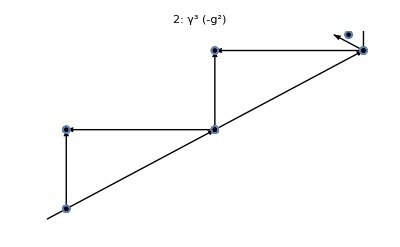
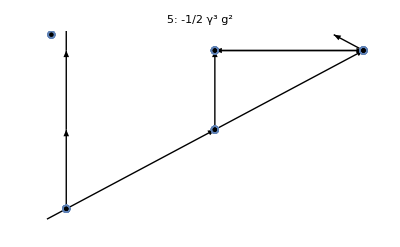
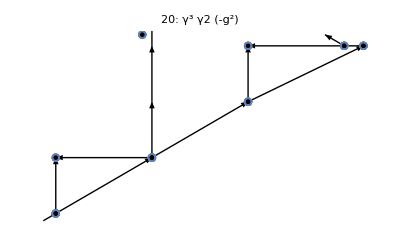
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
DrawFromContraction[TwoLoopBIS,"print"->False,"showEndLines"->True,"ImageSize"->Scaled[0.24]]
```

#### Laplacian integration with DDeatsG[] on TwoLoopBIS -> TwoLoopEaten

```mathematica
TwoLoopEaten=DDeatsG/@(List@@TwoLoopBIS);
```

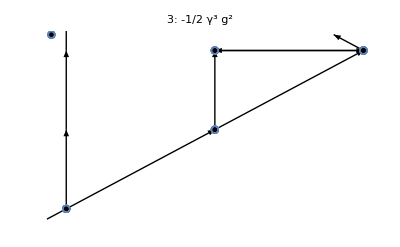
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
DrawFromContraction[TwoLoopEaten,"print"->False,"showEndLines"->True,"ImageSize"->Scaled[0.24]]
```

#### Get rid of trees with OnePI[] on TwoLoopEaten -> TwoLoop1PI

```mathematica
TwoLoop1PI=OnePI[Total@TwoLoopEaten,"print-onePIlist"->True];
```

{False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,True,False,False,True,True,True,True,True}

```mathematica
(List@@(Total@TwoLoop1PI/.χs[__]->1))[[1]]
```

g^2 γ^3 ϕs[x_3,t_4] ψs[x_2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_3,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3]

```mathematica
DrawFromContraction[List@@(Total@TwoLoop1PI/.χs[__]->1),"print"->False,"showEndLines"->False,"ImageSize"->Scaled[0.23]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

# Coupling renormalization

## 1-Loop: (b=1)

### OneLoopBackbone

#### Generate OneLoopγListCoupling

```mathematica
nInteractionVertices=1;
nγ2=0;
nγ2Minus=0;
endTime=nInteractionVertices+nInteractionVertices+1;

OneLoopγListCoupling=((*V[ϕs[Subscript[x, 0],Subscript[t, 1]]]**)Flatten[(Table[Table[Table[Spreadγ[nInteractionVertices+1,"print"->False,"nγ1δ"->(kkk-jjj),"nγ2"->iii,"nγ2Minus"->(jjj-iii),"evaluate"->False,"observable"->"g"],
{iii,0,jjj}],
{jjj,0,(kkk)}],
{kkk,0,nInteractionVertices}])
,3]
)
```

{{Vγ1,Vγ1},{Vγ1,Vγ1δ},{Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1},{Vγ1,Vγ1,Vγ2},{Vγ1,Vγ2,Vγ1}}

```mathematica
ΓString@OneLoopγListCoupling
```

ΓString[Vγ1,Vγ1]+ΓString[Vγ1,Vγ1δ]+ΓString[Vγ1,Vγ1,Vγ2]+ΓString[Vγ1,Vγ1,Vγ2Minus]+ΓString[Vγ1,Vγ2,Vγ1]+ΓString[Vγ1,Vγ2Minus,Vγ1]

#### Apply γ1FollowedByγ2p (Rule 2) to OneLoopγListRule1 -> OneLoopγListRule2

```mathematica
OneLoopγListRule2=γ1FollowedByγ2p[OneLoopγListCoupling]
```

{{Vγ1,Vγ1},{Vγ1,Vγ1δ},{Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1},{Vγ1,-Vγ1δ},{Vγ1,Vγg},{-Vγ1δ,Vγ1},{Vγg,Vγ1}}

```mathematica
ΓString@OneLoopγListRule2
```

ΓString[Vγ1,Vγ1]+ΓString[Vγ1,Vγg]-ΓString[Vγ1δ,Vγ1]+ΓString[Vγg,Vγ1]+ΓString[Vγ1,Vγ1,Vγ2Minus]+ΓString[Vγ1,Vγ2Minus,Vγ1]

#### Evaluate the vertices in OneLoopγListRule2 -> OneLoopγListEvaluated

```mathematica
OneLoopγListEvaluated=EvaluateVertices[OneLoopγListRule2]
```

{V[ϕs[x_0,t_1]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ δχs[x_2,1,2,t_2] ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_3,1,2,t_3]] ϕ[x_3,t_3] ϕs[x_3,t_4]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[-γ2 DD[δχs[x_2,1,2,t_2]] ϕ[x_2,t_2] ϕs[x_2,t_3]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],-V[ϕs[x_0,t_1]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ δχs[x_2,1,2,t_2] ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[g γ δχs[x_2,1,2,t_2] ϕ[x_2,t_2] ϕs[x_2,t_3] χ[x_2,1,α_67326,t_2] χs[x_2,1,α_67326,t_2]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]],-V[ϕs[x_0,t_1]] V[γ δχs[x_1,1,2,t_1] ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[g γ δχs[x_1,1,2,t_1] ϕ[x_1,t_1] ϕs[x_1,t_2] χ[x_1,1,α_81116,t_1] χs[x_1,1,α_81116,t_1]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]]}

#### Contract ϕ in OneLoopγListEvaluated -> OneLoopBackbone

```mathematica
OneLoopγListEvaluated;

AbsoluteTiming[OneLoopBackbone=List@@(Total@(WickContractionSpaceVerticesMODfaster[#,"fields"->FieldsNamesGenerator[{ϕ}], "endTime"->(endTime+1),"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->False,"FreeAction"->NONE,"maxContractions"->100]&/@%))]
```

{0.0282247,{g γ^2 δχs[x_2,1,2,t_2] ϕs[x_2,t_3] χ[x_2,1,α_67326,t_2] χs[x_2,1,α_67326,t_2] ψs[x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2],g γ^2 δχs[x_1,1,2,t_1] ϕs[x_2,t_3] χ[x_1,1,α_81116,t_1] χs[x_1,1,α_81116,t_1] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2],γ^2 ϕs[x_2,t_3] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2],-γ^2 δχs[x_1,1,2,t_1] ϕs[x_2,t_3] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2],-γ^2 γ2 DD[δχs[x_3,1,2,t_3]] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],-γ^2 γ2 DD[δχs[x_2,1,2,t_2]] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3]}}

```mathematica
DrawFromContraction[(OneLoopBackbone),"print"->False,"showEndLines"->True,"ImageSize"->300]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

### OneLoop: contraction form OneLoopBackbone

```mathematica
SpreadInteractions[nInteractionVertices,"endTime"->(endTime+1),"Vγ2δ"->True]
```

V[-g χ[x_11,i_65104,α_65104,t_3] χs[x_11,i_65104,α_65104,t_3] ψ[x_11,t_3]]+V[-g χ[x_21,i_91095,α_91095,t_2] χs[x_21,i_91095,α_91095,t_2] ψ[x_21,t_2]]+V[-g χ[x_31,i_55474,α_55474,t_1] χs[x_31,i_55474,α_55474,t_1] ψ[x_31,t_1]]

```mathematica
nInteractionVertices=2;
nγ2=0;
nγ2Minus=0;
endTime=nInteractionVertices+nγ2+nγ2Minus+1;

(List@@(Plus@@Expand[(OneLoopBackbone*(SpreadInteractions[nInteractionVertices,"endTime"->(endTime+1),"Vγ2δ"->True])*(*Vψχ[Subscript[x,endTime+100],endTime+1]*)δχs[Subscript[x, endTime+1],1,2,Subscript[t, endTime+1]])])
);


AbsoluteTiming[OneLoop=Plus@@(WickContractionSpaceVerticesMODfaster[#, "endTime"->(endTime+1),"print"->False,"fields"->FieldsNamesGenerator[{χ,ψ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True,"maxContractions"->100]&/@%)/.ψs[__]->0]
```

{5.90453,-g^2 γ^2 ϕs[x_2,t_3] χs[x_1,1,2,t_4] χs[x_2,1,2,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_4,t_4] G_χ[x_2,x_2,t_2] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4]-g^2 γ^2 γ2 DD[G_χ[x_2,x_3,t_3]] ϕs[x_3,t_4] χs[x_1,1,2,t_4] χs[x_2,1,2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3]-g^2 γ^2 ϕs[x_2,t_3] χs[x_1,1,2,t_1] χs[x_2,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_1,t_1] G_χ[x_2,x_4,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]-g^2 γ^2 γ2 DD[G_χ[x_1,x_3,t_3]] ϕs[x_3,t_4] χs[x_1,1,2,t_3] χs[x_2,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_2,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]+g^2 γ^2 ϕs[x_2,t_3] χs[x_2,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_4,t_4] G_χ[x_2,x_1,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]+g^2 γ^2 ϕs[x_2,t_3] χs[x_1,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_2,t_4] G_χ[x_2,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]-g^2 γ^2 γ2 DD[G_χ[x_1,x_2,t_2]] ϕs[x_3,t_4] χs[x_1,1,2,t_2] χs[x_3,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_3,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_3,x_3,t_4]}

```mathematica
OneLoop=OneLoop/.Subscript[G, χ][Subscript[x, a_],Subscript[x, 4],Subscript[t, 4]]:>χ[Subscript[x, a],Subscript[t, 4]];
DrawFromContraction[%,"print"->False,"showEndLines"->True,"ImageSize"->Scaled[0.3]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
(* This looks ok, let's see 2-Loop*)
```

```mathematica
DDeatsG[OneLoop];
DrawFromContraction[%,"print"->False,"showEndLines"->True,"ImageSize"->Scaled[0.3]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

## 1-Loop: (b generical)

### OneLoopBackbone

#### Generate OneLoopγListCoupling

```mathematica
nInteractionVertices=1;
nγ2=0;
nγ2Minus=0;
endTime=nInteractionVertices+nInteractionVertices+1;

OneLoopγListCoupling=((*V[ϕs[Subscript[x, 0],Subscript[t, 1]]]**)Flatten[(Table[Table[Table[Spreadγ[nInteractionVertices+1,"print"->False,"nγ1δ"->(kkk-jjj),"nγ2"->iii,"nγ2Minus"->(jjj-iii),"evaluate"->False,"observable"->"g"],
{iii,0,jjj}],
{jjj,0,(kkk)}],
{kkk,0,nInteractionVertices}])
,3]
)
```

{{Vγ1,Vγ1},{Vγ1,Vγ1δ},{Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1},{Vγ1,Vγ1,Vγ2},{Vγ1,Vγ2,Vγ1}}

```mathematica
ΓString@OneLoopγListCoupling
```

ΓString[{Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ1δ}]+ΓString[{Vγ1,Vγ1,Vγ2}]+ΓString[{Vγ1,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγ2,Vγ1}]+ΓString[{Vγ1,Vγ2Minus,Vγ1}]

#### Apply γ1FollowedByγ2p (Rule 2) to OneLoopγListRule1 -> OneLoopγListRule2

```mathematica
OneLoopγListRule2=γ1FollowedByγ2p[OneLoopγListCoupling]
```

{{Vγ1,Vγ1},{Vγ1,Vγ1δ},{Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1},{Vγ1,-Vγ1δ},{Vγ1,Vγg},{-Vγ1δ,Vγ1},{Vγg,Vγ1}}

```mathematica
ΓString@OneLoopγListRule2
```

ΓString[{Vγ1,Vγ1}]+ΓString[{Vγ1,Vγg}]-ΓString[{Vγ1δ,Vγ1}]+ΓString[{Vγg,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγ2Minus,Vγ1}]

#### Evaluate the vertices in OneLoopγListRule2 -> OneLoopγListEvaluated

```mathematica
expandedInb=Expandb[ΓString@OneLoopγListRule2]
```

ΓString[{Vγ1,Vγ1}]+ΓString[{Vγ1,Vγg}]-ΓString[{Vγ1δ,Vγ1}]+ΓString[{Vγg,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγ1,Vγ2Minus2}]+ΓString[{Vγ1,Vγ2Minus,Vγ1}]+ΓString[{Vγ1,Vγ2Minus2,Vγ1}]

```mathematica
ΓStringExtract/@(List@@expandedInb)
```

{{Vγ1,Vγ1},{Vγ1,Vγg},{-Vγ1δ,-Vγ1},{Vγg,Vγ1},{Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus2},{Vγ1,Vγ2Minus,Vγ1},{Vγ1,Vγ2Minus2,Vγ1}}

```mathematica
OneLoopγListEvaluatedb=EvaluateVertices[ΓStringExtract/@(List@@expandedInb)]
```

{V[ϕs[x_0,t_1]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[g γ δχs[x_2,1,2,t_2] ϕ[x_2,t_2] ϕs[x_2,t_3] χ[x_2,1,α_19917,t_2] χs[x_2,1,α_19917,t_2]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]],V[ϕs[x_0,t_1]] V[b γ δχs[x_1,1,1,t_1] ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[g γ δχs[x_1,1,2,t_1] ϕ[x_1,t_1] ϕs[x_1,t_2] χ[x_1,1,α_1689,t_1] χs[x_1,1,α_1689,t_1]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[-b γ2 DD[δχs[x_3,1,2,t_3]] ϕ[x_3,t_3] ϕs[x_3,t_4]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[-1/2 b2 γ2 DD[δχs[x_3,1,1,t_3] δχs[x_3,2,2,t_3]] ϕ[x_3,t_3] ϕs[x_3,t_4]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_2,t_2] ϕs[x_2,t_3] ψs[x_2,t_3]],V[ϕs[x_0,t_1]] V[-b γ2 DD[δχs[x_2,1,2,t_2]] ϕ[x_2,t_2] ϕs[x_2,t_3]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]],V[ϕs[x_0,t_1]] V[-1/2 b2 γ2 DD[δχs[x_2,1,1,t_2] δχs[x_2,2,2,t_2]] ϕ[x_2,t_2] ϕs[x_2,t_3]] V[γ ϕ[x_1,t_1] ϕs[x_1,t_2] ψs[x_1,t_2]] V[γ ϕ[x_3,t_3] ϕs[x_3,t_4] ψs[x_3,t_4]]}

#### Contract ϕ in OneLoopγListEvaluated -> OneLoopBackboneb

```mathematica
OneLoopγListEvaluatedb;

AbsoluteTiming[OneLoopBackboneb=List@@(Total@(WickContractionSpaceVerticesMODfaster[#,"fields"->FieldsNamesGenerator[{ϕ}], "endTime"->(endTime+1),"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->False,"FreeAction"->NONE,"maxContractions"->100]&/@%))]
```

{0.030725,{g γ^2 δχs[x_2,1,2,t_2] ϕs[x_2,t_3] χ[x_2,1,α_19917,t_2] χs[x_2,1,α_19917,t_2] ψs[x_1,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2],g γ^2 δχs[x_1,1,2,t_1] ϕs[x_2,t_3] χ[x_1,1,α_1689,t_1] χs[x_1,1,α_1689,t_1] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2],γ^2 ϕs[x_2,t_3] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2],b γ^2 δχs[x_1,1,1,t_1] ϕs[x_2,t_3] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2],-b γ^2 γ2 DD[δχs[x_3,1,2,t_3]] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],-1/2 b2 γ^2 γ2 DD[δχs[x_3,1,1,t_3] δχs[x_3,2,2,t_3]] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],-b γ^2 γ2 DD[δχs[x_2,1,2,t_2]] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],-1/2 b2 γ^2 γ2 DD[δχs[x_2,1,1,t_2] δχs[x_2,2,2,t_2]] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_3,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3]}}

```mathematica
(OneLoopBackboneb)[[6]]
%/.DD[δχs[Subscript[x, a_],A___,Subscript[t, c_]]δχs[Subscript[x, a_],B___,Subscript[t, c_]]]:>{Δ[Subscript[x, a-0.1],Subscript[x, a],Subscript[t, c]],δχs[Subscript[x, a-0.1],A,Subscript[t, c]]δχs[Subscript[x, a-0.1],B,Subscript[t, c]]}
```

-1/2 b2 γ^2 γ2 DD[δχs[x_3,1,1,t_3] δχs[x_3,2,2,t_3]] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3]

{-1/2 b2 γ^2 γ2 Δ[x_2.9,x_3,t_3] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3],-1/2 b2 γ^2 γ2 δχs[x_2.9,1,1,t_3] δχs[x_2.9,2,2,t_3] ϕs[x_3,t_4] ψs[x_1,t_2] ψs[x_2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3]}

```mathematica
DrawFromContraction[(OneLoopBackboneb),"print"->False,"showEndLines"->True,"ImageSize"->300]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

### OneLoop: contraction form OneLoopBackbone

```mathematica
nInteractionVertices=2;
nγ2=0;
nγ2Minus=0;
endTime=nInteractionVertices+nγ2+nγ2Minus+1;

(List@@(Plus@@Expand[(OneLoopBackboneb*(SpreadInteractions[nInteractionVertices,"endTime"->(endTime+1),"Vγ2δ"->True])*(*Vψχ[Subscript[x,endTime+100],endTime+1]*)δχs[Subscript[x, endTime+1],1,2,Subscript[t, endTime+1]])])
);


AbsoluteTiming[OneLoopb=Plus@@(WickContractionSpaceVerticesMODfaster[#, "endTime"->(endTime+1),"print"->False,"fields"->FieldsNamesGenerator[{χ,ψ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True,"maxContractions"->100]&/@%)/.ψs[__]->0]
```

{8.85686,-g^2 γ^2 ϕs[x_2,t_3] χs[x_1,1,2,t_4] χs[x_2,1,2,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_4,t_4] G_χ[x_2,x_2,t_2] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4]-b g^2 γ^2 γ2 DD[G_χ[x_2,x_3,t_3]] ϕs[x_3,t_4] χs[x_1,1,2,t_4] χs[x_2,1,2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3]-g^2 γ^2 ϕs[x_2,t_3] χs[x_1,1,2,t_1] χs[x_2,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_1,t_1] G_χ[x_2,x_4,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]-b g^2 γ^2 γ2 DD[G_χ[x_1,x_3,t_3]] ϕs[x_3,t_4] χs[x_1,1,2,t_3] χs[x_2,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_2,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]+g^2 γ^2 ϕs[x_2,t_3] χs[x_2,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_4,t_4] G_χ[x_2,x_1,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]+g^2 γ^2 ϕs[x_2,t_3] χs[x_1,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_χ[x_1,x_2,t_4] G_χ[x_2,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]-b g^2 γ^2 γ2 DD[G_χ[x_1,x_2,t_2]] ϕs[x_3,t_4] χs[x_1,1,2,t_2] χs[x_3,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_3,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_3,x_3,t_4]}

```mathematica
OneLoopb=OneLoopb/.Subscript[G, χ][Subscript[x, a_],Subscript[x, 4],Subscript[t, 4]]:>χ[Subscript[x, a],Subscript[t, 4]];
DrawFromContraction[%,"print"->False,"showEndLines"->True,"ImageSize"->Scaled[0.3]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
(* This looks ok, let's see 2-Loop*)
```

```mathematica
DDeatsG[OneLoopb];
DrawFromContraction[%,"print"->False,"showEndLines"->True,"ImageSize"->Scaled[0.3]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
(*OK, CHECK 2LOOP NOW*)
```

## 2-Loop: (b generical)

### TwoLoopBackbone

#### Generate TwoLoopγListCoupling

```mathematica
nInteractionVertices=2;
nγ2=0;
nγ2Minus=0;
endTime=nInteractionVertices+nInteractionVertices+1;

TwoLoopγListCoupling=((*V[ϕs[Subscript[x, 0],Subscript[t, 1]]]**)Flatten[(Table[Table[Table[Spreadγ[nInteractionVertices+1,"print"->False,"nγ1δ"->(kkk-jjj),"nγ2"->iii,"nγ2Minus"->(jjj-iii),"evaluate"->False,"observable"->"g"],
{iii,0,jjj}],
{jjj,0,(kkk)}],
{kkk,0,nInteractionVertices}])
,3]
)
```

{{Vγ1,Vγ1,Vγ1},{Vγ1,Vγ1,Vγ1δ},{Vγ1,Vγ1δ,Vγ1},{Vγ1,Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,Vγ1},{Vγ1,Vγ2Minus,Vγ1,Vγ1},{Vγ1,Vγ1,Vγ1,Vγ2},{Vγ1,Vγ1,Vγ2,Vγ1},{Vγ1,Vγ2,Vγ1,Vγ1},{Vγ1,Vγ1δ,Vγ1δ},{Vγ1,Vγ1,Vγ1δ,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,Vγ1δ},{Vγ1,Vγ1δ,Vγ1,Vγ2Minus},{Vγ1,Vγ1δ,Vγ2Minus,Vγ1},{Vγ1,Vγ2Minus,Vγ1,Vγ1δ},{Vγ1,Vγ2Minus,Vγ1δ,Vγ1},{Vγ1,Vγ1,Vγ1δ,Vγ2},{Vγ1,Vγ1,Vγ2,Vγ1δ},{Vγ1,Vγ1δ,Vγ1,Vγ2},{Vγ1,Vγ1δ,Vγ2,Vγ1},{Vγ1,Vγ2,Vγ1,Vγ1δ},{Vγ1,Vγ2,Vγ1δ,Vγ1},{Vγ1,Vγ1,Vγ1,Vγ2Minus,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,Vγ1,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,Vγ2Minus,Vγ1},{Vγ1,Vγ2Minus,Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1,Vγ2Minus,Vγ1},{Vγ1,Vγ2Minus,Vγ2Minus,Vγ1,Vγ1},{Vγ1,Vγ1,Vγ1,Vγ2,Vγ2Minus},{Vγ1,Vγ1,Vγ1,Vγ2Minus,Vγ2},{Vγ1,Vγ1,Vγ2,Vγ1,Vγ2Minus},{Vγ1,Vγ1,Vγ2,Vγ2Minus,Vγ1},{Vγ1,Vγ1,Vγ2Minus,Vγ1,Vγ2},{Vγ1,Vγ1,Vγ2Minus,Vγ2,Vγ1},{Vγ1,Vγ2,Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ2,Vγ1,Vγ2Minus,Vγ1},{Vγ1,Vγ2,Vγ2Minus,Vγ1,Vγ1},{Vγ1,Vγ2Minus,Vγ1,Vγ1,Vγ2},{Vγ1,Vγ2Minus,Vγ1,Vγ2,Vγ1},{Vγ1,Vγ2Minus,Vγ2,Vγ1,Vγ1},{Vγ1,Vγ1,Vγ1,Vγ2,Vγ2},{Vγ1,Vγ1,Vγ2,Vγ1,Vγ2},{Vγ1,Vγ1,Vγ2,Vγ2,Vγ1},{Vγ1,Vγ2,Vγ1,Vγ1,Vγ2},{Vγ1,Vγ2,Vγ1,Vγ2,Vγ1},{Vγ1,Vγ2,Vγ2,Vγ1,Vγ1}}

```mathematica
ΓString@TwoLoopγListCoupling
```

ΓString[{Vγ1,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ1δ}]+ΓString[{Vγ1,Vγ1δ,Vγ1}]+ΓString[{Vγ1,Vγ1δ,Vγ1δ}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγ1,Vγ1δ,Vγ2}]+ΓString[{Vγ1,Vγ1,Vγ1δ,Vγ2Minus}]+ΓString[{Vγ1,Vγ1,Vγ2,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2,Vγ1δ}]+ΓString[{Vγ1,Vγ1,Vγ2Minus,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus,Vγ1δ}]+ΓString[{Vγ1,Vγ1δ,Vγ1,Vγ2}]+ΓString[{Vγ1,Vγ1δ,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγ1δ,Vγ2,Vγ1}]+ΓString[{Vγ1,Vγ1δ,Vγ2Minus,Vγ1}]+ΓString[{Vγ1,Vγ2,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2,Vγ1,Vγ1δ}]+ΓString[{Vγ1,Vγ2,Vγ1δ,Vγ1}]+ΓString[{Vγ1,Vγ2Minus,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus,Vγ1,Vγ1δ}]+ΓString[{Vγ1,Vγ2Minus,Vγ1δ,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2,Vγ2}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2,Vγ2Minus}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus,Vγ2}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus,Vγ2Minus}]+ΓString[{Vγ1,Vγ1,Vγ2,Vγ1,Vγ2}]+ΓString[{Vγ1,Vγ1,Vγ2,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγ1,Vγ2,Vγ2,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2,Vγ2Minus,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus,Vγ1,Vγ2}]+ΓString[{Vγ1,Vγ1,Vγ2Minus,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγ1,Vγ2Minus,Vγ2,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus,Vγ2Minus,Vγ1}]+ΓString[{Vγ1,Vγ2,Vγ1,Vγ1,Vγ2}]+ΓString[{Vγ1,Vγ2,Vγ1,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγ2,Vγ1,Vγ2,Vγ1}]+ΓString[{Vγ1,Vγ2,Vγ1,Vγ2Minus,Vγ1}]+ΓString[{Vγ1,Vγ2,Vγ2,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2,Vγ2Minus,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus,Vγ1,Vγ1,Vγ2}]+ΓString[{Vγ1,Vγ2Minus,Vγ1,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγ2Minus,Vγ1,Vγ2,Vγ1}]+ΓString[{Vγ1,Vγ2Minus,Vγ1,Vγ2Minus,Vγ1}]+ΓString[{Vγ1,Vγ2Minus,Vγ2,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus,Vγ2Minus,Vγ1,Vγ1}]

#### Apply γ1FollowedByγ2p (Rule 2) to TwoLoopγListRule1 -> TwoLoopγListRule2

```mathematica
TwoLoopγListRule2=γ1FollowedByγ2p[TwoLoopγListCoupling]
```

{{Vγ1,Vγ1,Vγ1},{Vγ1,Vγ1,Vγ1δ},{Vγ1,Vγ1δ,Vγ1},{Vγ1,Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,Vγ1},{Vγ1,Vγ2Minus,Vγ1,Vγ1},{Vγ1,Vγ1,-Vγ1δ},{Vγ1,Vγ1,Vγg},{Vγ1,-Vγ1δ,Vγ1},{Vγ1,Vγg,Vγ1},{-Vγ1δ,Vγ1,Vγ1},{Vγg,Vγ1,Vγ1},{Vγ1,Vγ1δ,Vγ1δ},{Vγ1,Vγ1,Vγ1δ,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,Vγ1δ},{Vγ1,Vγ1δ,Vγ1,Vγ2Minus},{Vγ1,Vγ1δ,Vγ2Minus,Vγ1},{Vγ1,Vγ2Minus,Vγ1,Vγ1δ},{Vγ1,Vγ2Minus,Vγ1δ,Vγ1},{Vγ1,Vγ1,Vγ1δ,Vγ2},{Vγ1,-Vγ1δ,Vγ1δ},{Vγ1,Vγg,Vγ1δ},{Vγ1,Vγ1δ,-Vγ1δ},{Vγ1,Vγ1δ,Vγg},{Vγ1,Vγ1δ,Vγ2,Vγ1},{-Vγ1δ,Vγ1,Vγ1δ},{Vγg,Vγ1,Vγ1δ},{-Vγ1δ,Vγ1δ,Vγ1},{Vγg,Vγ1δ,Vγ1},{Vγ1,Vγ1,Vγ1,Vγ2Minus,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,Vγ1,Vγ2Minus},{Vγ1,Vγ1,Vγ2Minus,Vγ2Minus,Vγ1},{Vγ1,Vγ2Minus,Vγ1,Vγ1,Vγ2Minus},{Vγ1,Vγ2Minus,Vγ1,Vγ2Minus,Vγ1},{Vγ1,Vγ2Minus,Vγ2Minus,Vγ1,Vγ1},{Vγ1,Vγ1,-Vγ1δ,Vγ2Minus},{Vγ1,Vγ1,Vγg,Vγ2Minus},{Vγ1,Vγ1,Vγ1,Vγ2Minus,Vγ2},{Vγ1,-Vγ1δ,Vγ1,Vγ2Minus},{Vγ1,Vγg,Vγ1,Vγ2Minus},{Vγ1,-Vγ1δ,Vγ2Minus,Vγ1},{Vγ1,Vγg,Vγ2Minus,Vγ1},{Vγ1,Vγ1,Vγ2Minus,-Vγ1δ},{Vγ1,Vγ1,Vγ2Minus,Vγg},{Vγ1,Vγ1,Vγ2Minus,Vγ2,Vγ1},{-Vγ1δ,Vγ1,Vγ1,Vγ2Minus},{Vγg,Vγ1,Vγ1,Vγ2Minus},{-Vγ1δ,Vγ1,Vγ2Minus,Vγ1},{Vγg,Vγ1,Vγ2Minus,Vγ1},{-Vγ1δ,Vγ2Minus,Vγ1,Vγ1},{Vγg,Vγ2Minus,Vγ1,Vγ1},{Vγ1,Vγ2Minus,Vγ1,-Vγ1δ},{Vγ1,Vγ2Minus,Vγ1,Vγg},{Vγ1,Vγ2Minus,-Vγ1δ,Vγ1},{Vγ1,Vγ2Minus,Vγg,Vγ1},{Vγ1,Vγ2Minus,Vγ2,Vγ1,Vγ1},{Vγ1,Vγ1,-Vγ1δ,Vγ2},{Vγ1,Vγ1,Vγg,Vγ2},{Vγ1,-Vγ1δ,Vγ1,Vγ2},{Vγ1,Vγg,Vγ1,Vγ2},{Vγ1,-Vγ1δ,Vγ2,Vγ1},{Vγ1,Vγg,Vγ2,Vγ1},{-Vγ1δ,Vγ1,Vγ1,Vγ2},{Vγg,Vγ1,Vγ1,Vγ2},{-Vγ1δ,Vγ1,Vγ2,Vγ1},{Vγg,Vγ1,Vγ2,Vγ1},{-Vγ1δ,Vγ2,Vγ1,Vγ1},{Vγg,Vγ2,Vγ1,Vγ1}}

```mathematica
ΓString@TwoLoopγListRule2
```

ΓString[{Vγ1,Vγ1}]+ΓString[{Vγ1,Vγg}]-ΓString[{Vγ1δ,Vγ1}]+ΓString[{Vγg,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγ2Minus,Vγ1}]

#### SuppressFirstδχ in ΓString@TwoLoopγListRule2 -> SuppressedFirstδχ

```mathematica
SuppressedFirstδχ=SuppressFirstδχ[ΓString@TwoLoopγListRule2]
```

ΓString[{Vγ1,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγg}]-ΓString[{Vγ1,Vγ1δ,Vγ1δ}]+ΓString[{Vγ1,Vγ1δ,Vγg}]+ΓString[{Vγ1,Vγg,Vγ1}]+ΓString[{Vγ1,Vγg,Vγ1δ}]+ΓString[{Vγg,Vγ1,Vγ1}]+ΓString[{Vγg,Vγ1,Vγ1δ}]+ΓString[{Vγg,Vγ1δ,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγ1,Vγ2Minus,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus,Vγg}]+ΓString[{Vγ1,Vγ1,Vγg,Vγ2}]+ΓString[{Vγ1,Vγ1,Vγg,Vγ2Minus}]-ΓString[{Vγ1,Vγ1δ,Vγ1,Vγ2}]+ΓString[{Vγ1,Vγ2Minus,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus,Vγ1,Vγg}]+ΓString[{Vγ1,Vγ2Minus,Vγg,Vγ1}]+ΓString[{Vγ1,Vγg,Vγ1,Vγ2}]+ΓString[{Vγ1,Vγg,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγg,Vγ2,Vγ1}]+ΓString[{Vγ1,Vγg,Vγ2Minus,Vγ1}]+ΓString[{Vγg,Vγ1,Vγ1,Vγ2}]+ΓString[{Vγg,Vγ1,Vγ1,Vγ2Minus}]+ΓString[{Vγg,Vγ1,Vγ2,Vγ1}]+ΓString[{Vγg,Vγ1,Vγ2Minus,Vγ1}]+ΓString[{Vγg,Vγ2,Vγ1,Vγ1}]+ΓString[{Vγg,Vγ2Minus,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus,Vγ2}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus,Vγ2Minus}]+ΓString[{Vγ1,Vγ1,Vγ2Minus,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγ1,Vγ2Minus,Vγ2,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus,Vγ2Minus,Vγ1}]+ΓString[{Vγ1,Vγ2Minus,Vγ1,Vγ1,Vγ2Minus}]+ΓString[{Vγ1,Vγ2Minus,Vγ1,Vγ2Minus,Vγ1}]+ΓString[{Vγ1,Vγ2Minus,Vγ2,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus,Vγ2Minus,Vγ1,Vγ1}]

#### Expandb in SuppressedFirstδχ -> expandedInb

```mathematica
expandedInb=Expandb[SuppressedFirstδχ]/.δχ^n_/;n>=3:>0/.δχ:>1;
```

```mathematica
expandedInb
```

ΓString[{Vγ1,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγg}]-ΓString[{Vγ1,Vγ1δ1,Vγ1δ1}]-ΓString[{Vγ1,Vγ1δ1,Vγ1δ2}]+ΓString[{Vγ1,Vγ1δ1,Vγg}]-ΓString[{Vγ1,Vγ1δ2,Vγ1δ1}]+ΓString[{Vγ1,Vγ1δ2,Vγg}]+ΓString[{Vγ1,Vγg,Vγ1}]+ΓString[{Vγ1,Vγg,Vγ1δ1}]+ΓString[{Vγ1,Vγg,Vγ1δ2}]+ΓString[{Vγg,Vγ1,Vγ1}]+ΓString[{Vγg,Vγ1,Vγ1δ1}]+ΓString[{Vγg,Vγ1,Vγ1δ2}]+ΓString[{Vγg,Vγ1δ1,Vγ1}]+ΓString[{Vγg,Vγ1δ2,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus1}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus2}]+ΓString[{Vγ1,Vγ1,Vγ2Minus1,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus1,Vγg}]+ΓString[{Vγ1,Vγ1,Vγ2Minus2,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus2,Vγg}]+ΓString[{Vγ1,Vγ1,Vγg,Vγ21}]+ΓString[{Vγ1,Vγ1,Vγg,Vγ22}]+ΓString[{Vγ1,Vγ1,Vγg,Vγ2Minus1}]+ΓString[{Vγ1,Vγ1,Vγg,Vγ2Minus2}]-ΓString[{Vγ1,Vγ1δ1,Vγ1,Vγ21}]-ΓString[{Vγ1,Vγ1δ1,Vγ1,Vγ22}]-ΓString[{Vγ1,Vγ1δ2,Vγ1,Vγ21}]+ΓString[{Vγ1,Vγ2Minus1,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus1,Vγ1,Vγg}]+ΓString[{Vγ1,Vγ2Minus1,Vγg,Vγ1}]+ΓString[{Vγ1,Vγ2Minus2,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus2,Vγ1,Vγg}]+ΓString[{Vγ1,Vγ2Minus2,Vγg,Vγ1}]+ΓString[{Vγ1,Vγg,Vγ1,Vγ21}]+ΓString[{Vγ1,Vγg,Vγ1,Vγ22}]+ΓString[{Vγ1,Vγg,Vγ1,Vγ2Minus1}]+ΓString[{Vγ1,Vγg,Vγ1,Vγ2Minus2}]+ΓString[{Vγ1,Vγg,Vγ21,Vγ1}]+ΓString[{Vγ1,Vγg,Vγ22,Vγ1}]+ΓString[{Vγ1,Vγg,Vγ2Minus1,Vγ1}]+ΓString[{Vγ1,Vγg,Vγ2Minus2,Vγ1}]+ΓString[{Vγg,Vγ1,Vγ1,Vγ21}]+ΓString[{Vγg,Vγ1,Vγ1,Vγ22}]+ΓString[{Vγg,Vγ1,Vγ1,Vγ2Minus1}]+ΓString[{Vγg,Vγ1,Vγ1,Vγ2Minus2}]+ΓString[{Vγg,Vγ1,Vγ21,Vγ1}]+ΓString[{Vγg,Vγ1,Vγ22,Vγ1}]+ΓString[{Vγg,Vγ1,Vγ2Minus1,Vγ1}]+ΓString[{Vγg,Vγ1,Vγ2Minus2,Vγ1}]+ΓString[{Vγg,Vγ21,Vγ1,Vγ1}]+ΓString[{Vγg,Vγ22,Vγ1,Vγ1}]+ΓString[{Vγg,Vγ2Minus1,Vγ1,Vγ1}]+ΓString[{Vγg,Vγ2Minus2,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus1,Vγ21}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus1,Vγ22}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus1,Vγ2Minus1}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus1,Vγ2Minus2}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus2,Vγ21}]+ΓString[{Vγ1,Vγ1,Vγ1,Vγ2Minus2,Vγ2Minus1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus1,Vγ1,Vγ2Minus1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus1,Vγ1,Vγ2Minus2}]+ΓString[{Vγ1,Vγ1,Vγ2Minus1,Vγ21,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus1,Vγ22,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus1,Vγ2Minus1,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus1,Vγ2Minus2,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus2,Vγ1,Vγ2Minus1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus2,Vγ21,Vγ1}]+ΓString[{Vγ1,Vγ1,Vγ2Minus2,Vγ2Minus1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus1,Vγ1,Vγ1,Vγ2Minus1}]+ΓString[{Vγ1,Vγ2Minus1,Vγ1,Vγ1,Vγ2Minus2}]+ΓString[{Vγ1,Vγ2Minus1,Vγ1,Vγ2Minus1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus1,Vγ1,Vγ2Minus2,Vγ1}]+ΓString[{Vγ1,Vγ2Minus1,Vγ21,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus1,Vγ22,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus1,Vγ2Minus1,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus1,Vγ2Minus2,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus2,Vγ1,Vγ1,Vγ2Minus1}]+ΓString[{Vγ1,Vγ2Minus2,Vγ1,Vγ2Minus1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus2,Vγ21,Vγ1,Vγ1}]+ΓString[{Vγ1,Vγ2Minus2,Vγ2Minus1,Vγ1,Vγ1}]

#### Evaluate the vertices in expandedInb -> TwoLoopγListEvaluated

```mathematica
TwoLoopγListEvaluatedb=EvaluateVertices[ΓStringExtract/@(List@@expandedInb)]
```

#### Contract ϕ in TwoLoopγListEvaluated -> TwoLoopBackboneb

```mathematica
TwoLoopγListEvaluatedb;

AbsoluteTiming[TwoLoopBackboneb=List@@(Total@(WickContractionSpaceVerticesMODfaster[#,"fields"->FieldsNamesGenerator[{ϕ}], "endTime"->(endTime+1),"print"->False,"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->False,"FreeAction"->NONE,"maxContractions"->100]&/@%));]
```

{4.95562,Null}

```mathematica
DrawFromContraction[(TwoLoopBackboneb),"print"->False,"showEndLines"->True,"ImageSize"->300]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

### TwoLoop: contraction form TwoLoopBackbone

```mathematica
nInteractionVertices=2;
nγ2=0;
nγ2Minus=0;
endTime=nInteractionVertices+nγ2+nγ2Minus+1;

skele=(List@@(Plus@@Expand[(TwoLoopBackboneb*(SpreadInteractions[nInteractionVertices,"endTime"->(endTime+1),"Vγ2δ"->True])*(*Vψχ[Subscript[x,endTime+100],endTime+1]*)δχs[Subscript[x, endTime+1],1,2,Subscript[t, endTime+1]])])
);


AbsoluteTiming[TwoLoopb=Plus@@(Table[WickContractionSpaceVerticesMODfaster[skele[[i]], "endTime"->(endTime+1),"print"->False,"fields"->FieldsNamesGenerator[{χ,ψ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True,"maxContractions"->100]/.ψs[__]->0,{i,1,500}]);]
```

{67.7903,Null}

```mathematica
AbsoluteTiming[TwoLoopb501=Plus@@(Table[WickContractionSpaceVerticesMODfaster[skele[[i]], "endTime"->(endTime+1),"print"->False,"fields"->FieldsNamesGenerator[{χ,ψ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True,"maxContractions"->100]/.ψs[__]->0,{i,501,800}]);]
```

{226.302,Null}

```mathematica
AbsoluteTiming[TwoLoopb801=Plus@@(Table[WickContractionSpaceVerticesMODfaster[skele[[i]], "endTime"->(endTime+1),"print"->False,"fields"->FieldsNamesGenerator[{χ,ψ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True,"maxContractions"->100]/.ψs[__]->0,{i,801,900}]);]
```

{1908.94,Null}

```mathematica
AbsoluteTiming[TwoLoopb901=Plus@@(Table[WickContractionSpaceVerticesMODfaster[skele[[i]], "endTime"->(endTime+1),"print"->False,"fields"->FieldsNamesGenerator[{χ,ψ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True,"maxContractions"->100]/.ψs[__]->0,{i,901,1000}]);]
```

{989.324,Null}

```mathematica
AbsoluteTiming[TwoLoopb1001=Plus@@(Table[WickContractionSpaceVerticesMODfaster[skele[[i]], "endTime"->(endTime+1),"print"->False,"fields"->FieldsNamesGenerator[{χ,ψ}],"δrule"->True,"δruleExternal"->True,"n_χ"->(-1),"n_α"->(0),"killψ"->True,"maxContractions"->100]/.ψs[__]->0,{i,1001,Length[skele]}]);]
```

{1385.9,Null}

```mathematica
overall=TwoLoopb+TwoLoopb501+TwoLoopb801+TwoLoopb901+TwoLoopb1001
```

1/2 g^3 γ^3 ϕs[x_3,t_4] χs[x_1,1,2,t_4] χs[x_3,1,2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_4,t_4] G_χ[x_2,x_3,t_3] G_χ[x_3,x_2,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3]+1/2 g^3 γ^3 ϕs[x_3,t_4] χs[x_1,1,2,t_4] χs[x_2,1,2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_4,t_4] G_χ[x_2,x_3,t_3] G_χ[x_3,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3]+b g^3 γ^3 ϕs[x_3,t_4] χs[x_1,1,1,t_2] χs[x_2,1,2,t_4] χs[x_3,1,2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_2] G_χ[x_2,x_4,t_4] G_χ[x_3,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]+1/2 g^3 γ^3 ϕs[x_3,t_4] χs[x_2,1,2,t_4] χs[x_3,1,2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_4,t_4] G_χ[x_3,x_1,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]+1/2 g^3 γ^3 ϕs[x_3,t_4] χs[x_1,1,2,t_3] χs[x_2,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_4,t_4] G_χ[x_3,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]+g^3 γ^3 ϕs[x_3,t_4] χs[x_2,1,2,t_4] χs[x_3,1,2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_4,t_4] G_χ[x_2,x_1,t_4] G_χ[x_3,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]+g^3 γ^3 ϕs[x_3,t_4] χs[x_1,1,2,t_4] χs[x_3,1,2,t_3] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_4] G_χ[x_2,x_4,t_4] G_χ[x_3,x_3,t_3] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4]+1/2 g^3 γ^3 ϕs[x_3,t_4] χs[x_2,1,2,t_2] χs[x_3,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_2] G_χ[x_2,x_1,t_2] G_χ[x_3,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_3,x_3,t_4]+1/2 g^3 γ^3 ϕs[x_3,t_4] χs[x_1,1,2,t_2] χs[x_3,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_2,t_2] G_χ[x_2,x_2,t_2] G_χ[x_3,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_3,x_3,t_4]+b g^3 γ^3 ϕs[x_3,t_4] χs[x_1,1,1,t_3] χs[x_2,1,2,t_2] χs[x_3,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_3] G_χ[x_2,x_2,t_2] G_χ[x_3,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_3,x_3,t_4]+g^3 γ^3 ϕs[x_3,t_4] χs[x_2,1,2,t_2] χs[x_3,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_4,t_4] G_χ[x_2,x_2,t_2] G_χ[x_3,x_1,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_3,x_3,t_4]+g^3 γ^3 ϕs[x_3,t_4] χs[x_1,1,2,t_4] χs[x_2,1,2,t_2] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_3,t_4] G_χ[x_2,x_2,t_2] G_χ[x_3,x_4,t_4] G_ψ[x_1,x_1,t_2] G_ψ[x_1,x_1,t_3] G_ψ[x_1,x_1,t_4] G_ψ[x_3,x_3,t_4]+b g^3 γ^3 ϕs[x_3,t_4] χs[x_1,1,2,t_1] χs[x_2,1,1,t_3] χs[x_3,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_1,t_1] G_χ[x_2,x_3,t_3] G_χ[x_3,x_4,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_3,x_3,t_4]+g^3 γ^3 ϕs[x_3,t_4] χs[x_1,1,2,t_1] χs[x_3,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_1,t_1] G_χ[x_2,x_4,t_4] G_χ[x_3,x_2,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4] G_ψ[x_3,x_3,t_4]+g^3 γ^3 ϕs[x_3,t_4] χs[x_1,1,2,t_1] χs[x_2,1,2,t_4] G_ϕ[x_1,x_0,t_1] G_ϕ[x_2,x_1,t_2] G_ϕ[x_3,x_2,t_3] G_χ[x_1,x_1,t_1] G_χ[x_2,x_3,t_4] G_χ[x_3,x_4,t_4] G_ψ[x_2,x_2,t_3] G_ψ[x_2,x_2,t_4] G_ψ[x_3,x_3,t_4]

```mathematica
overall=overall/.Subscript[G, χ][Subscript[x, a_],Subscript[x, 5],Subscript[t, 5]]:>χ[Subscript[x, a],Subscript[t, 5]];
DrawFromContraction[%,"print"->False,"showEndLines"->True,"ImageSize"->Scaled[0.3]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
DDeatsG[overall];
DrawFromContraction[%,"print"->False,"showEndLines"->True,"ImageSize"->Scaled[0.3]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
(* NO SOME THINGS ARE WRONG !!!*)
```